# #DO NOT Run Complete Notebook at once might takes hours to run the full code

```mathematica
Needs["DifferentialEquations`NDSolveProblems`"];
Needs["DifferentialEquations`NDSolveUtilities`"];
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"];
Needs["GUIKit`"];
(*RangeOfProjectile[Throwing Arm length a,weight arm length b,Weigth pendulum length c,height of pivot d,length of sling l,mass 1 m1,mass to be thrown m2,release angle trigger rA,show log  1 or 0]
This function takes the variables of the trebuchet and provides all the significant values in the output.
this implementstion of the process as a function Simpliflies iteration process and makes the optimization faster
slog values allows you to print the values of variables in current iteration the logging if switched off by default and can be
enabled by passing value 1*)
iniTheta = 170Degree;
initialAlfa = 10Degree;
RangeOfProjectile[a_,b_,c_,d_,l_,m1_,m2_,rA_,Slog_:0] :=(designDelay = 5;
ϕ[t_]=θ[t] - ArcCos[(d+a*Cos[θ[t]])/l];
x1[t_]=b Sin[θ[t]]-c Sin[θ[t]+γ[t]];
y1[t_]=-b Cos[θ[t]]+c Cos[θ[t]+γ[t]];
x2[t_]=-a Sin[θ[t]]+l Sin[θ[t]-ϕ[t]];
y2[t_]=a Cos[θ[t]]-l Cos[θ[t]-ϕ[t]];
Te1= 1/2 m1((D[x1[t],t]^2) +(D[y1[t],t]^2))+1/2 m2((D[x2[t],t]^2) +(D[y2[t],t]^2));
V1=m1 g y1[t]+m2 g y2[t];

L1 = Te1-V1;


Eqn1={D[D[L1, θ'[t]], t]-D[L1, θ[t]]==0 ,D[D[L1,γ'[t]], t]-D[L1,γ[t]]==0,θ[0]==iniTheta,θ'[0]==0,γ[0]==initialAlfa,γ'[0]==0,WhenEvent[θ[t]==ArcCos[(l-d)/a]+0.00001,"StopIntegration"]};

sol1= NDSolve[Eqn1,{γ,θ},{t,0,2}];
end = Last[First[InterpolatingFunctionDomain[First[θ/.sol1]]]];
datat=Table[Flatten[{t,Evaluate[{θ[t]}/.sol1]}],{t,0,end,0.0005}];
datag=Table[Flatten[{t,Evaluate[{γ[t]}/.sol1]}],{t,0,end,0.0005}];
dataa=Table[Flatten[{t,Evaluate[{ϕ[t]}/.sol1]}],{t,0,end,0.0005}];

thE = First[θ[end]/.sol1];
thvE = First[θ'[end]/.sol1];
gmE =First[γ[end]/.sol1];
gmvE =First[γ'[end]/.sol1];
alfE =First[ϕ[end]/.sol1];
alfEV =First[ϕ'[end]/.sol1];;
x2[t_]:=-a Sin[θ[t]]+l Sin[θ[t]-α[t]];
y2[t_]:=a Cos[θ[t]]-l Cos[θ[t]-α[t]];

Te=1/2 m1((D[x1[t],t]^2) +(D[y1[t],t]^2))+1/2 m2((D[x2[t],t]^2) +(D[y2[t],t]^2));
V=m1 g y1[t]+m2 g y2[t]; 
L = Te-V;
Eqn2={D[D[L, α'[t]], t]-D[L, α[t]]==0 ,D[D[L, θ'[t]], t]-D[L, θ[t]]==0 ,D[D[L,γ'[t]], t]-D[L,γ[t]]==0,θ[end]==thE,θ'[end]==thvE,γ[end]==gmE,γ'[end]==gmvE,α[end]==alfE,α'[end]==alfEV,WhenEvent[α[t]==rA,"StopIntegration"]};
sol2= NDSolve[Eqn2,{γ,θ,α},{t,end,20}];
end2 = Last[First[InterpolatingFunctionDomain[First[θ/.sol2]]]];

datat2=Table[Flatten[{t,Evaluate[{θ[t]}/.sol2]}],{t,end,end2,0.0005}];

datag2=Table[Flatten[{t,Evaluate[{γ[t]}/.sol2]}],{t,end,end2,0.0005}];

dataa2=Table[Flatten[{t,Evaluate[{α[t]}/.sol2]}],{t,end,end2,0.0005}];


SOL={{θ->Interpolation[Join[datat,datat2]],
γ->Interpolation[Join[datag,datag2]],α-> Interpolation[Join[dataa,dataa2]]}};
theta = First[θ[end2-0.001]/.SOL];
thetaDot =First[θ'[end2-0.001]/.SOL];
 alfa = First[α[end2-0.001]/.SOL];
alfaDot =First[α'[end2-0.001]/.SOL];

RelseaseAngle  =ArcTan[(First[y2'[end2-0.001]/.SOL])/(First[x2'[end2-0.001]/.SOL])];

ReleaseVelocity =((-l Cos[alfa-theta] (alfaDot-thetaDot)-a Cos[theta] thetaDot)^2+(l Sin[alfa-theta] (alfaDot-thetaDot)-a Sin[theta] thetaDot)^2)^(1/2);
If[Slog > 0,Print[{a,b,c,d,l,m1,m2,rA}],klp = a(*do nothing*)];
{solution -> SOL,range-> (ReleaseVelocity ^2 * Sin[2*RelseaseAngle])/g,releaseangle-> RelseaseAngle /Degree,relVel -> ReleaseVelocity,Plot_α-> Plot[α[t]/.SOL,{t,0,end2},AxesLabel -> {"t(Seconds)","α[t]"},PlotRange -> Full],
Plot_θ-> Plot[θ[t]/.SOL,{t,0,end2},AxesLabel -> {"t(Seconds)","θ[t]"},PlotRange -> Full],
Plot_γ-> Plot[γ[t]/.SOL,{t,0,end2},AxesLabel -> {"t(Seconds)","γ[t]"},PlotRange -> Full],
Plot_dα -> Plot[α'[t]/.SOL,{t,0,end2},AxesLabel -> {"t(Seconds)","α'[t]"},PlotRange -> Full],
Plot_dθ-> Plot[θ'[t]/.SOL,{t,0,end2},AxesLabel -> {"t(Seconds)","θ'[t]"},PlotRange -> Full],
Plot_dγ -> Plot[γ'[t]/.SOL,{t,0,end2},AxesLabel -> {"t(Seconds)","γ'[t]"},PlotRange -> Full],Para_P-> ParametricPlot[{{First[x2[t]/.SOL],First[y2[t]/.SOL]},{First[x1[t]/.SOL],First[y1[t]/.SOL]}},{t,0,end2},AxesLabel -> {"x","y"},PlotLegends-> {"m2","m1"}]}

)
```

```mathematica
g=9.81;
a=4;
b=1;
c=0.5;
d=5;
l=4;
m1=133;
m2=1;

rA = 2.75;
```

## Initial Solution

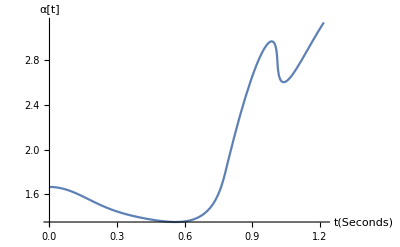
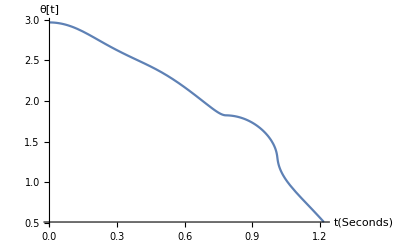
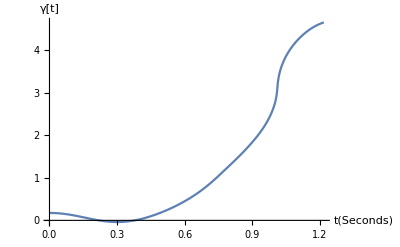
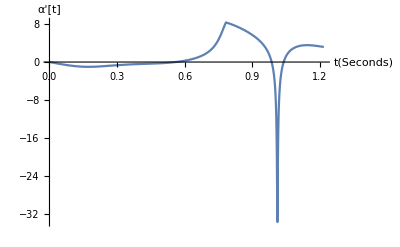
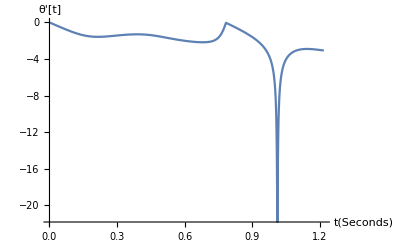
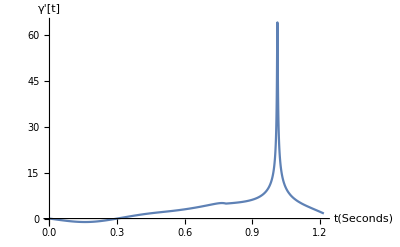
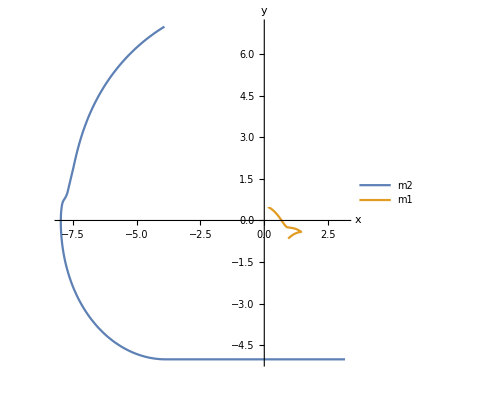
{solution→{{θ→InterpolatingFunction[{{0., 1.21877}}, <>],γ→InterpolatingFunction[{{0., 1.21877}}, <>],α→InterpolatingFunction[{{0., 1.21877}}, <>]}},range→121.193,releaseangle→29.579,relVel→37.2118,Plot_α→-Graphics-,Plot_θ→-Graphics-,Plot_γ→-Graphics-,Plot_dα→-Graphics-,Plot_dθ→-Graphics-,Plot_dγ→-Graphics-,Para_P→-Graphics-}

```mathematica
Solution = RangeOfProjectile[4,b,c,d,4,m1,m2,3.14]
```

## Validation

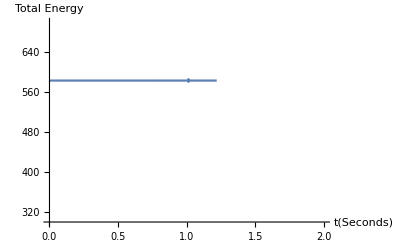

```mathematica
Plot[Te+V/.SOL,{t,0,end2},AxesLabel -> {"t(Seconds)","Total Energy"} ,PlotRange -> {{0,2},{300,700}}]
```

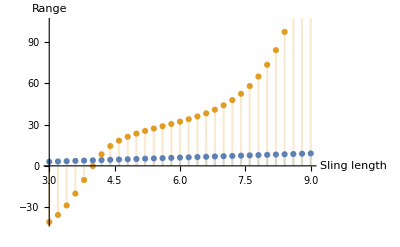

```mathematica
DiscretePlot[{x,range/.RangeOfProjectile[6,b,c,d,x,m1,m2,3.13]},{x,3,9,0.2},AxesLabel -> {"Sling length","Range"}]
```

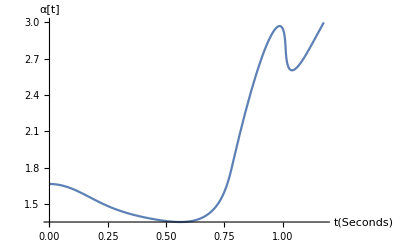
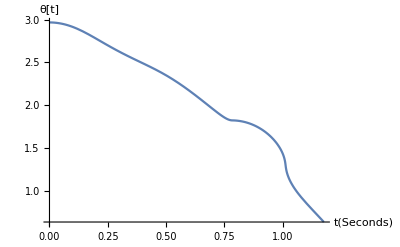
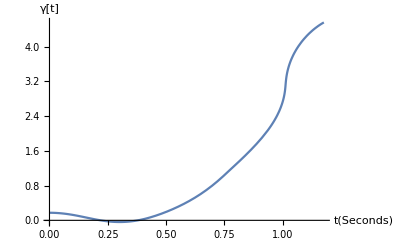
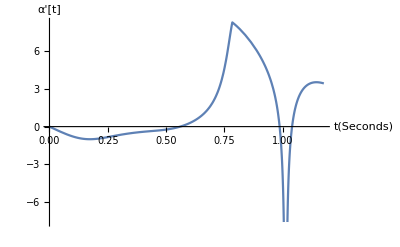
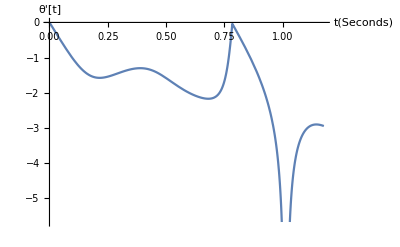
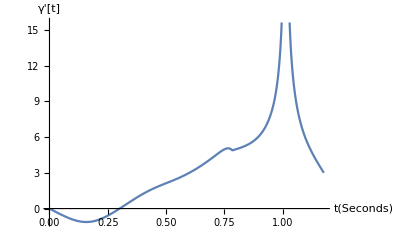
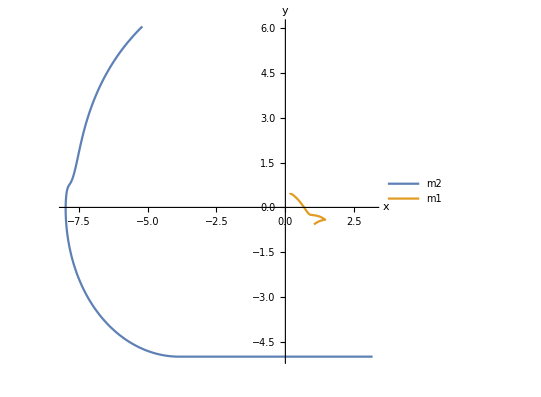
{solution→{{θ→InterpolatingFunction[{{0., 1.17677}}, <>],γ→InterpolatingFunction[{{0., 1.17677}}, <>],α→InterpolatingFunction[{{0., 1.17677}}, <>]}},range→140.957,releaseangle→42.3589,relVel→37.265,Plot_α→-Graphics-,Plot_θ→-Graphics-,Plot_γ→-Graphics-,Plot_dα→-Graphics-,Plot_dθ→-Graphics-,Plot_dγ→-Graphics-,Para_P→-Graphics-}

```mathematica
(*Calling function  RangeOfProjectile[Throwing Arm length a,weight arm length b,Weigth pendulum length c,height of pivot d,length of sling l,mass 1 m1,mass to be thrown m2,release angle trigger rA, Show log  1 or 0]*)
Solution = RangeOfProjectile[4,b,c,d,4,m1,m2,3]
```

```mathematica
(*Calling function  RangeOfProjectile[Throwing Arm length a,weight arm length b,Weigth pendulum length c,height of pivot d,length of sling l,mass 1 m1,mass to be thrown m2,release angle trigger rA, Show log  1 or 0]*)
```

```mathematica
Release Angle iteration
```

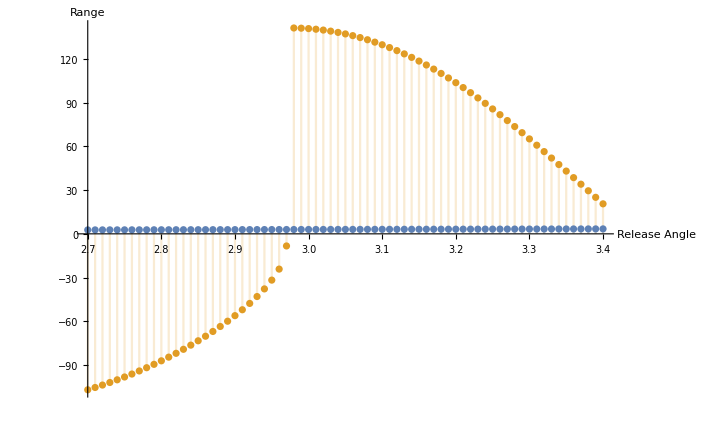

```mathematica
DiscretePlot[{x,range/.RangeOfProjectile[4,b,c,d,4,m1,m2,x,1]},{x,2.7,3.4,0.01},AxesLabel -> {"Release Angle","Range"}]
```

```mathematica
Sling length iteration
```

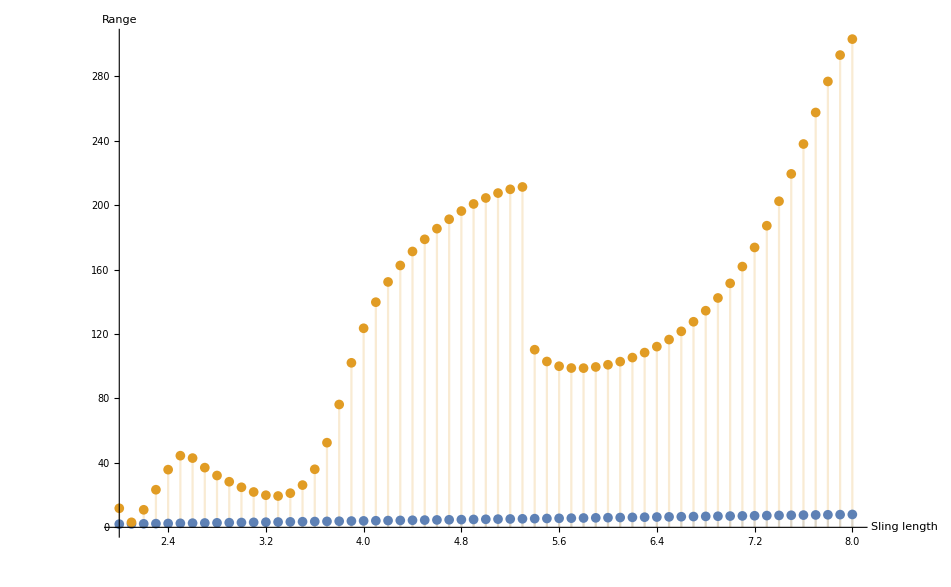

```mathematica
(*RangeOfProjectile[Throwing Arm length a,weight arm length b,Weigth pendulum length c,height of pivot d,length of sling l,mass 1 m1,mass to be thrown m2,release angle trigger rA]*)
DiscretePlot[{x,range/.RangeOfProjectile[4,b,c,d,x,m1,m2,3.13]},{x,2,8,0.1},AxesLabel -> {"Sling length","Range"}]
```

```mathematica
Throwing arm length iteration
```

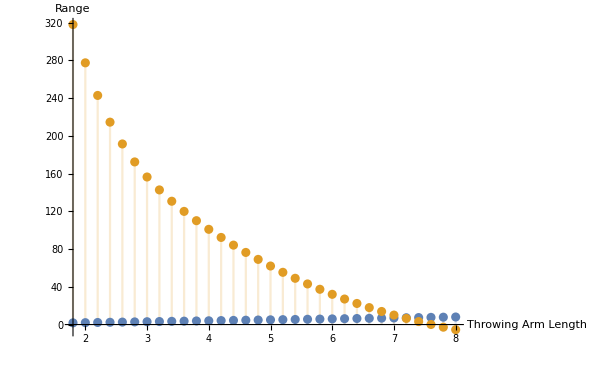

```mathematica
(*RangeOfProjectile[Throwing Arm length a,weight arm length b,Weigth pendulum length c,height of pivot d,length of sling l,mass 1 m1,mass to be thrown m2,release angle trigger rA]*)
DiscretePlot[{x,range/.RangeOfProjectile[x,b,c,d,6,m1,m2,3.13,1]},{x,1.8,8,0.2},AxesLabel -> {"Throwing Arm Length","Range"}]
```

```mathematica
pendulum length iteration
(*RangeOfProjectile[Throwing Arm length a,weight arm length b,Weigth pendulum length c,height of pivot d,length of sling l,mass 1 m1,mass to be thrown m2,release angle trigger rA]*)
```

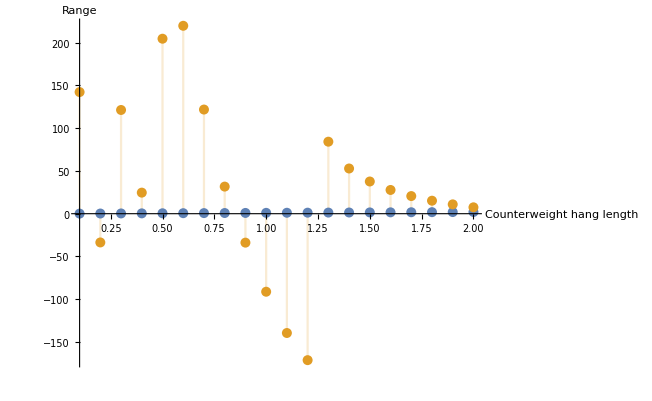

```mathematica
DiscretePlot[{x,range/.RangeOfProjectile[4,b,x,d,5,m1,m2,3.13]},{x,0.1,2,0.1},AxesLabel -> {"Counterweight hang length","Range"},PlotRange -> Full]
```

```mathematica
Test at choice of value from iteration
```

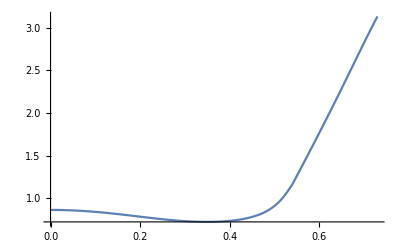
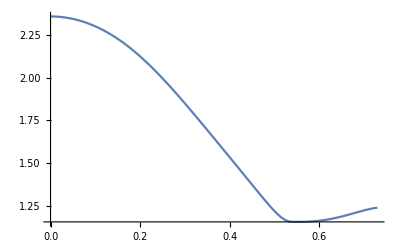
{solution→{{θ→InterpolatingFunction[{{0., 0.729963}}, <>],γ→InterpolatingFunction[{{0., 0.729963}}, <>],α→InterpolatingFunction[{{0., 0.729963}}, <>]}},range→183.453,Plot_α→-Graphics-,releaseangle→72.3875,relVel→55.8583,Plot_θ→-Graphics-,Plot_γ→

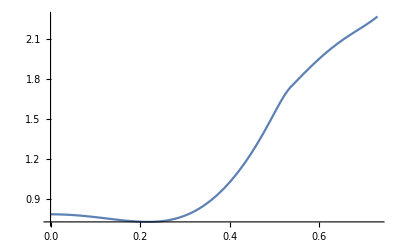
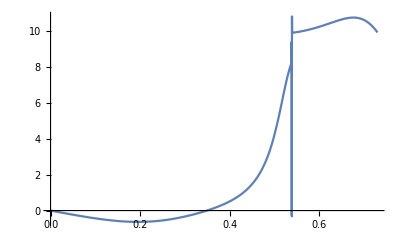
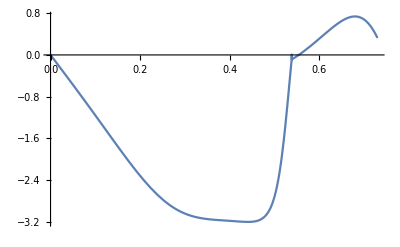
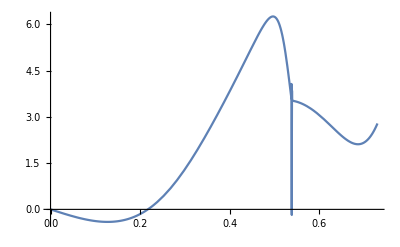
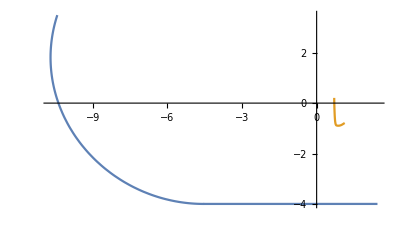
-Graphics-,Plot_dα→-Graphics-,Plot_dθ→-Graphics-,Plot_dγ→-Graphics-,Para_P→-Graphics-}

```mathematica
RangeOfProjectile[5,b,c,d,6,m1,m2,3.13]
```

```mathematica
release angle iteration again
```

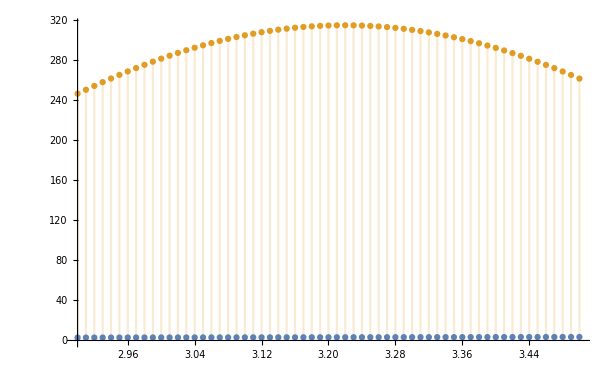

```mathematica
DiscretePlot[{x,range/.RangeOfProjectile[4,b,0.4,d,5,m1,m2,x]},{x,2.9,3.5,0.01},AxesLabel -> {"Release Angle","Range"}]
```

```mathematica
Test at choice of value from iteration
```

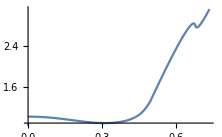
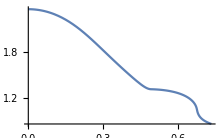
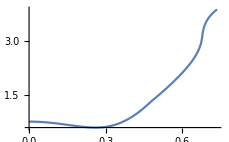
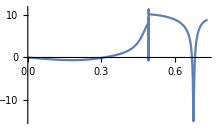
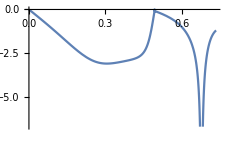
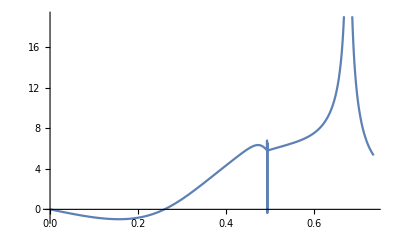
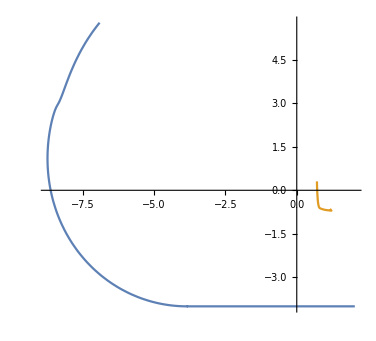
{solution→{{θ→InterpolatingFunction[{{0., 0.734999}}, <>],γ→InterpolatingFunction[{{0., 0.734999}}, <>],α→InterpolatingFunction[{{0., 0.734999}}, <>]}},range→309.6,Plot_α→-Graphics-,releaseangle→50.8574,relVel→55.6937,Plot_θ→-Graphics-,Plot_γ→-Graphics-,Plot_dα→-Graphics-,Plot_dθ→-Graphics-,Plot_dγ→-Graphics-,Para_P→-Graphics-}

```mathematica
RangeOfProjectile[4,b,0.4,d,5,m1,m2,3.13]
```

### 2D iteration across release angle and sling length

```mathematica
DiscretePlot3D[range/.RangeOfProjectile[4,b,0.4,d,x,m1,m2,y,1],{x, 2,8,0.4},{y,2.8,4,0.08},AxesLabel -> {"Sling Length","Release Angle","Range"}]
```

```mathematica
DiscretePlot3D[range/.RangeOfProjectile[y,b,0.4,d,x,m1,m2,3.13,1],{x,4,8,1},{y,3,9,1},AxesLabel -> {"Sling Length","ThrowArm","Range"}]
```

-Graphics3D-

```mathematica
DiscretePlot3D[range/.RangeOfProjectile[4,b,0.4,d,x,m1,m2,y],{x, 2,8,1},{y,2.8,4,0.2},AxesLabel -> {"Sling Length","Release Angle","Range"}]
```

NDSolve::ndsz: At t == 0.649932, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

```mathematica
data3d =Table[range/.RangeOfProjectile[z,b,0.4,d,x,m1,m2,y,1],{z,2,6,0.5},{y,2.8,3.3,0.1},{x,2,6,0.5}]
```

### Animation

```mathematica
Clear[pen]
```

```mathematica
pen[s_]:=Module[{g=g,a= 6.4,b=b,c=0.1,d=d,l=8,m1=m1,m2=m2,tmax=20,ptA,ptB,t ,ptm1,ptm2},
x1[t]=b Sin[θ[t]]-c Sin[θ[t]+γ[t]];
y1[t]=-b Cos[θ[t]]+c Cos[θ[t]+γ[t]];
x2[t]:=-a Sin[θ[t]]+l Sin[θ[t]-α[t]];
y2[t]:=a Cos[θ[t]]-l Cos[θ[t]-α[t]];
ptA={First[-a Sin[θ[s]]/.SOL],First[a Cos[θ[s]]/.SOL]};
ptB={First[b Sin[θ[s]]/.SOL],First[-b Cos[θ[s]]/.SOL]};
ptm1={First[x1[s]/.SOL],First[y1[s]/.SOL]};
ptm2={First[x2[s]/.SOL],First[y2[s]/.SOL]};
Show[Graphics[{Thickness[.01],Line[{{0,0},ptA}],PointSize[.03],Black,Point[ptA],Thickness[.01],Line[{{0,0},ptB}],PointSize[.03],Black,Point[ptB],Gray,PointSize[.06],Point[{0,0}],Black,PointSize[.04],Point[{0,0}],White,PointSize[.02],Point[{0,0}],Thickness[.005],Blue,Line[{ptB,ptm1}], PointSize[.05],Blue,Point[ptm1],Thickness[.005], Red, Line[{ptA,ptm2}],PointSize[.02], Red, Point[ptm2]}],Axes->False,Ticks->None,AxesStyle->GrayLevel[.5],PlotRange->{{-20,20},{-20,20}}]]
```

```mathematica
ptA={-a Cos[θ[s]-90 Degree],-a Sin[θ[s]-90 Degree]}/.SOL[[1]]
```

{-4 Sin[InterpolatingFunction[{{0., 0.775499}}, <>][s]],4 Cos[InterpolatingFunction[{{0., 0.775499}}, <>][s]]}

```mathematica
mov=Animate[pen[t],{t,0,end2},AnimationRate->0.15,RefreshRate->50]
```

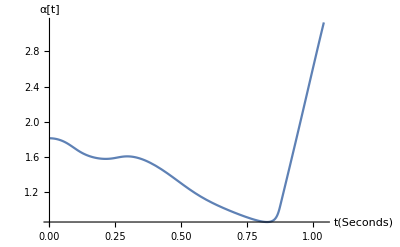
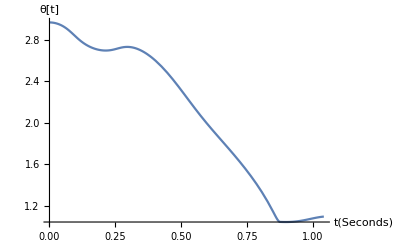
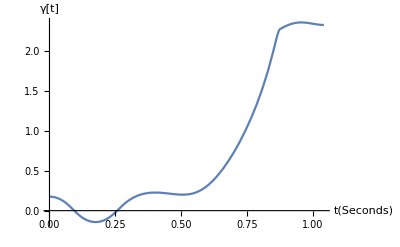
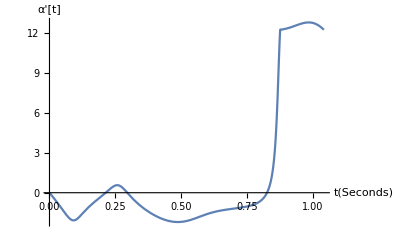
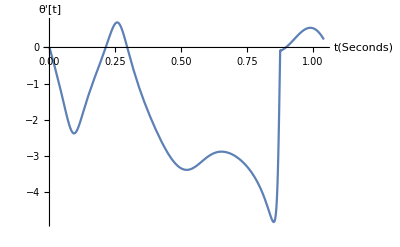
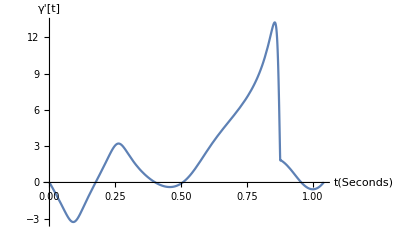
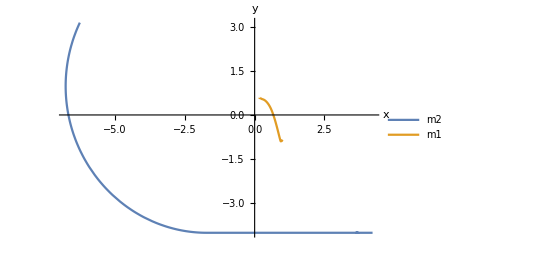
{solution→{{θ→InterpolatingFunction[{{0., 1.04175}}, <>],γ→InterpolatingFunction[{{0., 1.04175}}, <>],α→InterpolatingFunction[{{0., 1.04175}}, <>]}},range→284.205,releaseangle→64.2954,relVel→59.7245,Plot_α→-Graphics-,Plot_θ→-Graphics-,Plot_γ→-Graphics-,Plot_dα→-Graphics-,Plot_dθ→-Graphics-,Plot_dγ→-Graphics-,Para_P→-Graphics-}

```mathematica
RangeOfProjectile[2,b,0.4,4,5,m1,m2,3.13]
```

```mathematica
a =2;c =0.4;d =4;l =5;
```

```mathematica
data3dr2
```

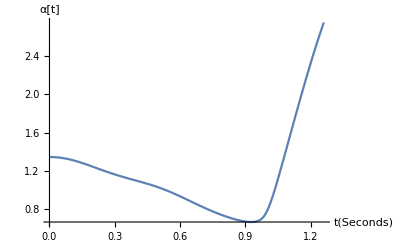
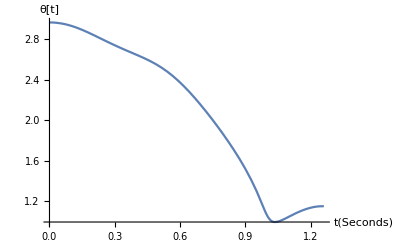
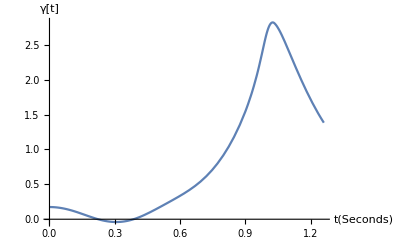
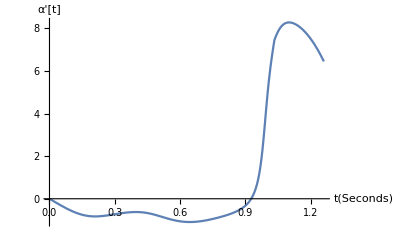
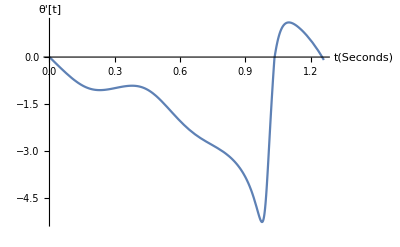
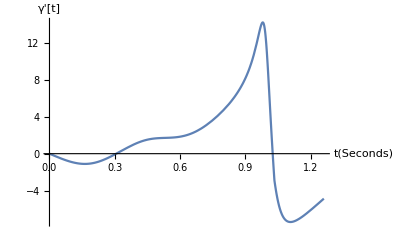
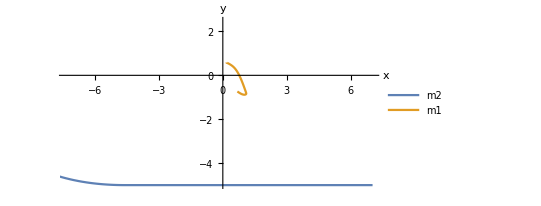
{solution→{{θ→InterpolatingFunction[{{0., 1.26034}}, <>],γ→InterpolatingFunction[{{0., 1.26034}}, <>],α→InterpolatingFunction[{{0., 1.26034}}, <>]}},range→14.9923,releaseangle→88.4887,relVel→52.8125,Plot_α→-Graphics-,Plot_θ→-Graphics-,Plot_γ→-Graphics-,Plot_dα→-Graphics-,Plot_dθ→-Graphics-,Plot_dγ→-Graphics-,Para_P→-Graphics-}

```mathematica
RangeOfProjectile[5.5,b,0.4,d,8,m1,m2,2.75,]
```

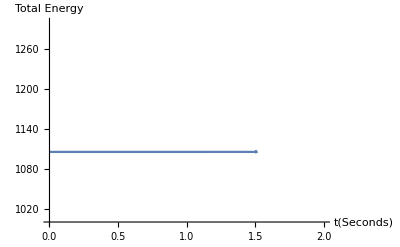

```mathematica
Plot[Te+V/.SOL,{t,0,end2},AxesLabel -> {"t(Seconds)","Total Energy"},PlotRange -> {{0,2},{1000,1300}}]
```

```mathematica
DiscretePlot[{x,range/.RangeOfProjectile[6.4,b,0.1,d,8,m1,m2,x]},{x,2,3.15,0.01},AxesLabel -> {"Release Angle","Range"}]
```

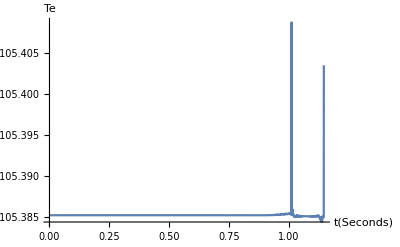

```mathematica
Plot[Te1+V1/.sol1,{t,0,end},AxesLabel -> {"t(Seconds)","Te"},PlotRange -> Full]
```

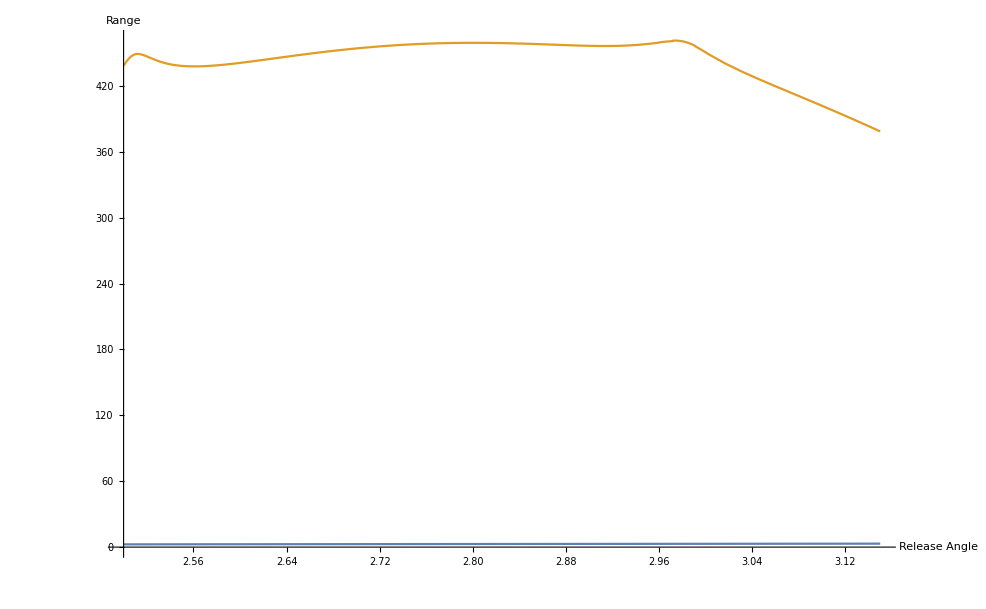

```mathematica
Plot[{x,range/.RangeOfProjectile[6.4,b,0.1,d,8,m1,m2,x,1]},{x,2.5,3.15},AxesLabel -> {"Release Angle","Range"}]
```

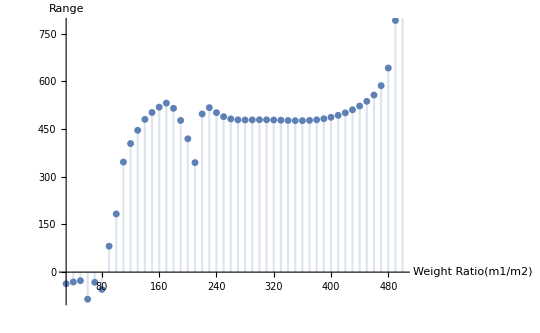

```mathematica
DiscretePlot[{range/.RangeOfProjectile[6.4,b,0.1,d,8,x,1,2.83,1]},{x,30,500,10},AxesLabel -> {"Weight Ratio(m1/m2)","Range"}]
```

```mathematica
sol1
```

{{γ→InterpolatingFunction[{{0., 2.}}, <>],θ→InterpolatingFunction[{{0., 2.}}, <>]}}

## 3-D and 4-D Iterations and Visualization

```mathematica
data3dr = Table[range/.RangeOfProjectile[z,b,0.4,d,x,m1,m2,y,1],{z,3,6,0.75},{y,2.8,3.4,0.15},{x,3,6,0.75}]
ListContourPlot3D[data3dr,DataRange->{{3,6},{2.8,3.4},{3,6}},Contours -> 5]
```

-Graphics3D-

```mathematica
(*DO not run the next cell Use the text data from below, it takes more that 2 Hours to run*)
```

```mathematica
data3dr2 = Table[range/.RangeOfProjectile[z,b,y,d,x,m1,m2,u,1],{z,4,8,0.8},{y,0.1,4.1,0.4},{x,3,8,0.5},{u,2.75,3.15, 0.08}]
```

{1}
 |  |  |  |

```mathematica
Labeled[ListDensityPlot3D[data3dr2[[All,All,All,1]],DataRange->{{4,8},{0.1,4.1},{3,8}},ColorFunction-> Hue,PlotLegends->Automatic,AxesLabel-> {"Sling Length","Pendulum Length","Throwing Arm Length"}],"Density Plot - Range of projectile at release angle 2.75",Top]
```

-Graphics3D-Density Plot - Range of projectile at release angle 2.75

```mathematica
Labeled[ListContourPlot3D[data3dr2[[All,All,All,1]],DataRange->{{4,8},{0.1,4.1},{3,8}},Contours -> 5,PlotLegends->"Expressions" ,AxesLabel-> {"Sling Length","Pendulum Length","Throwing Arm Length"}],"Contour Plot - Range of projectile at release angle 2.75",Top]
```

-Graphics3D-Contour Plot - Range of projectile at release angle 2.75

```mathematica
ListContourPlot3D[data3dr,DataRange->{{3,6},{2.8,3.4},{3,6}},Contours -> 10,PlotLegends->"Expressions" , AxesLabel->{"throwarm","releaseangle","Sling"}]
```

-Graphics3D-

```mathematica
Export["test3.dat",data3dr2]
```

test3.dat

```mathematica
Labeled[ListDensityPlot3D[data3dr2[[All,All,All,1]],DataRange->{{4,8},{0.1,4.1},{3,8}},ColorFunction->"TemperatureMap",PlotLegends->Automatic,AxesLabel-> {"Sling Length","Pendulum Length","Throwing Arm Length"}],"Range of projectile at release angle 2.75",Top]
Labeled[ListDensityPlot3D[data3dr2[[All,All,All,2]],DataRange->{{4,8},{0.1,4.1},{3,8}},PlotLegends->Automatic,ColorFunction->"TemperatureMap",AxesLabel-> {"Throwing Arm Length","Pendulum Length","Sling Length"}],"Range of projectile at release angle 2.83",Top]
Labeled[ListDensityPlot3D[data3dr2[[All,All,All,3]],DataRange->{{4,8},{0.1,4.1},{3,8}},PlotLegends->Automatic,ColorFunction->"TemperatureMap",AxesLabel-> {"Sling Length","Throwing Arm Length","Pendulum Length"}],"Range of projectile at release angle 2.91",Top]
Labeled[ListDensityPlot3D[data3dr2[[All,All,All,4]],DataRange->{{4,8},{0.1,4.1},{3,8}},PlotLegends->Automatic,ColorFunction->"TemperatureMap",AxesLabel-> {"Throwing Arm Length","Pendulum Length","Sling Length"}],"Range of projectile at release angle 2.99",Top]
Labeled[ListDensityPlot3D[data3dr2[[All,All,All,5]],DataRange->{{4,8},{0.1,4.1},{3,8}},PlotLegends->Automatic,ColorFunction->"TemperatureMap",AxesLabel-> {"Throwing Arm Length","Pendulum Length","Sling Length"}],"Range of projectile at release angle 3.07",Top]
Labeled[ListDensityPlot3D[data3dr2[[All,All,All,6]],DataRange->{{4,8},{0.1,4.1},{3,8}},PlotLegends->Automatic,ColorFunction->"TemperatureMap",AxesLabel-> {"Throwing Arm Length","Pendulum Length","Sling Length"}],"Range of projectile at release angle 3.15",Top]
```

```mathematica
-Graphics3D-"Range of projectile at release angle 2.75"
```

```mathematica
-Graphics3D-"Range of projectile at release angle 2.83"
```

-Graphics3D-Range of projectile at release angle 2.91

-Graphics3D-Range of projectile at release angle 2.99

-Graphics3D-Range of projectile at release angle 3.07

-Graphics3D-Range of projectile at release angle 3.15

```mathematica
ListDensityPlot3D[data3dr,DataRange->{{,6},{2.8,3.4},{3,6}},ColorFunction -> Hue,PlotLegends->"Expressions"]
```

-Graphics3D-

## Final Optimum Parameters and Run a = 6.4, b =1 , c = 0.1, d = 5, l = 8 , m1/m2 = 133, Release angle = 2.83

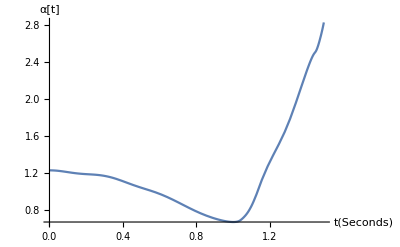
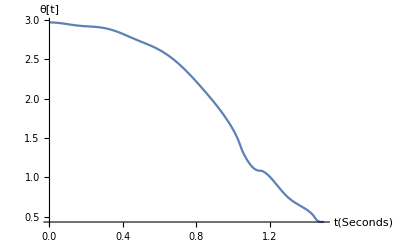
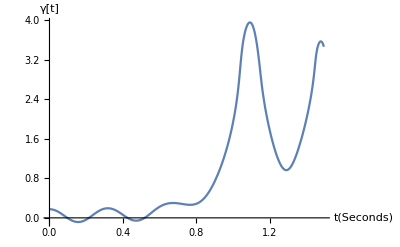
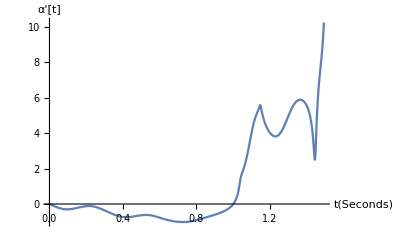
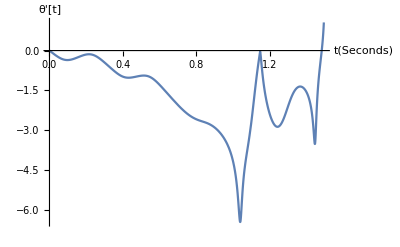
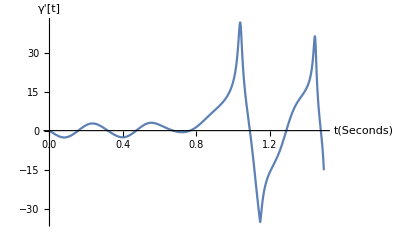
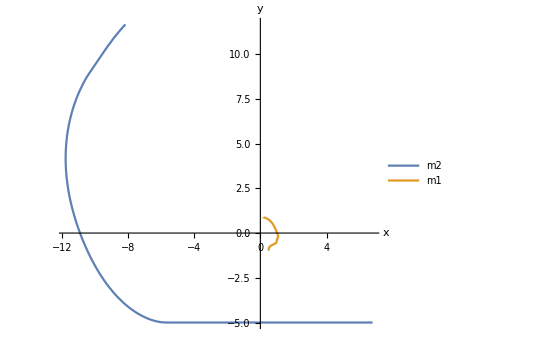
{solution→{{θ→InterpolatingFunction[{{0., 1.4937}}, <>],γ→InterpolatingFunction[{{0., 1.4937}}, <>],α→InterpolatingFunction[{{0., 1.4937}}, <>]}},range→458.928,releaseangle→45.0032,relVel→67.0976,Plot_α→-Graphics-,Plot_θ→-Graphics-,Plot_γ→-Graphics-,Plot_dα→-Graphics-,Plot_dθ→-Graphics-,Plot_dγ→-Graphics-,Para_P→-Graphics-}

```mathematica
RangeOfProjectile[6.4,b,0.1,d,8,m1,m2,2.83]
```

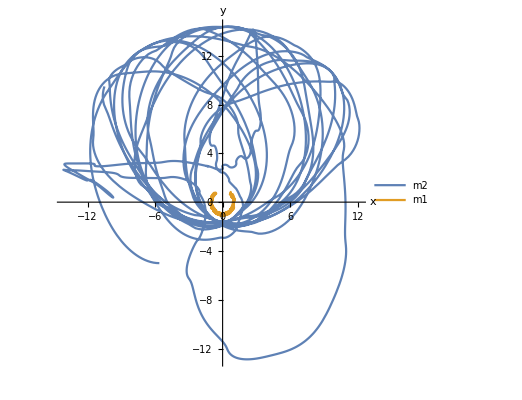

```mathematica
ParametricPlot[{{First[x2[t]/.sol2],First[y2[t]/.sol2]},{First[x1[t]/.sol2],First[y1[t]/.sol2]}},{t,end,20},AxesLabel -> {"x","y"},PlotLegends-> {"m2","m1"},PlotRange -> Full]
```

```mathematica
data3dr2 ={{{{-108.84608370465402,-110.32990175680465,-108.58101425445562,-103.65656364381587,-95.6945612734832,-84.90049761313259},{-150.6715855202484,-148.09707586334707,-141.67281188959777,-131.58679942395779,-118.14482457740965,-101.76494128328083},{-179.8058217442188,-170.01953344057793,-155.8178610256851,-137.62600655386174,-116.00167628061654,-91.61371700583399},{-174.23443658524093,-149.84798082149766,-120.634704212587,-87.37192560705272,-50.91579580180756,-12.048291829653788},{-34.4366239539016,-8.677091702642693,30.55375455961763,73.19384860716251,113.91768900198714,151.00320580348074},{161.29598212433262,209.6233780743599,251.44169984986533,284.4234965368433,272.25470351589155,235.2885166474378},{369.266649780707,339.5639712587829,299.6552092050974,251.7628433982405,198.1368923303568,140.6058705167982},{390.71529718934545,363.05216848015874,329.2470276193901,295.997633203591,297.2363492466073,205.76326679938225},{348.09194304676004,370.4805959743424,382.83117853886284,385.2025205458217,377.92068107813526,361.45952948593526},{285.99515147992696,247.95183440084904,317.3018074091503,348.9998801189783,359.5326045397758,360.045166714399},{-121.18815282831801,-184.01755932872743,-242.4624552759733,-295.11228154236295,-340.6905340380279,-378.07702189703093}},{{-57.2837417222325,-54.794089330421194,-48.638337489142124,-35.245476020398215,35.606832566148846,20.92749329478716},{-81.75715445584372,-72.94354273872285,-58.87706883149143,-34.38174081437694,41.48024247366462,21.10725683030568},{-98.31017687963387,-79.29877070701231,-52.130316794374245,141.24000203838338,134.78648686440263,118.65248444842834},{-102.60309152063492,-71.30205710766103,-28.252830575820695,164.45829817835994,175.46048512955693,178.9624021714774},{-99.81500006975583,-60.74861944683008,-14.89181687515722,54.36735072244051,193.41018014241365,207.22085396723176},{-101.18379341535407,-60.32342548949472,-17.23775803790072,26.87430958410896,70.79757615331765,113.48473044628757},{-104.99479421957587,-62.16218313876355,-17.980213996005336,26.39147844243265,69.76471731081014,110.9656966488604},{-98.52759072326575,-52.86221223217572,-6.382609787209325,39.79677515450629,84.56699030031818,126.86434337099023},{-66.07333056418648,-18.08476599622656,29.721045965814483,76.25247355691194,120.45557535049173,161.34615777442846},{14.845309165558225,63.714107363442324,110.49569188764652,154.0594552574153,193.34877795818946,227.40778828562173},{164.0282164752009,209.02602901412732,247.1628848343262,276.7319181482793,296.12311176495433,303.8814026174926}},{{-43.71513535570582,-42.31986378817547,-38.40106451344864,-30.777184027738812,-157.56508060668364,-151.7057957760918},{-47.74790654245171,-37.49956855865792,-164.8654025649763,-175.44530520762345,-181.28228773186046,-182.1403756016439},{-60.4715335866654,-94.56164255562663,-125.62590623951623,-152.47964128672692,-174.16231281873502,-189.94839321893906},{53.986849695823764,14.91452730512871,-25.40463751299737,-65.3211876351027,-103.21965835592034,-137.58568820843746},{156.02115619748767,121.93311823945109,83.43521557724813,41.87363870373506,-1.2983560759293977,-44.57312292117202},{236.27106064169735,210.56794516171973,178.60133025152416,141.33073679943305,99.88557717231495,55.527378189054104},{295.006955447383,280.0986639262368,257.9704489759881,229.1614058202222,194.41286551437312,154.6454614882358},{323.85688222106523,322.82761995325035,314.7222873421894,299.56116332374296,277.56398524274,249.15566146900758},{274.51262602085745,287.6269733180407,297.15312996271354,302.87376522423733,304.16791047419935,290.9861406309338},{188.68360425035948,223.70751371308725,255.9033387803072,281.5880574612445,299.65086683805663,310.1590615895943},{196.11782573818147,232.0841552584734,262.96738269545057,287.90345765655036,306.2133665380732,317.44651545327065}},{{-64.19564848392474,-65.37514359338022,-64.55923083327004,-61.80199498298273,-57.23579920279917,-51.05425044167086},{-80.6505063685964,-77.65212400660582,-72.21750971446232,-64.53282909225788,-54.86026108777258,-43.517933935289854},{-89.47072788175058,-80.52431061886784,-68.83563606653973,-54.74959868355883,-38.682864993447126,-21.097637896771403},{-86.42583066344397,-69.6449387280415,-49.993297575442305,-27.990473887211884,-4.193118596309688,20.902342768113222},{-66.34892185503149,-39.75552818247753,-10.325195426336329,21.398175151070113,55.348040639437215,97.04002336121022},{-23.635985833336278,14.807738255469102,56.53299760789407,104.12737781121373,-110.40090423975316,-143.21134035132815},{45.40151556976842,98.41711581056282,177.586393982725,31.16569880239041,-13.740353763446336,-58.257293423347996},{134.12491022625758,214.40132970580822,180.493266779806,138.93114691418623,93.33975901630687,45.10269336978553},{203.1960365987917,273.7331566584935,263.0783307673872,228.94422712505974,188.6402571073673,143.33538109107602},{216.38388811710192,258.4754768723636,292.95913971338086,317.68717139948666,219.13417407495416,175.02732914412914},{196.9569787710091,236.01029822405374,269.31761607037896,296.015240394285,315.3966068976635,326.93853811679645}},{{-77.97578534784633,-79.94593153403106,-79.64156329506348,-77.10415268829065,-72.46890438553135,-65.95440869483483},{-99.89421122349769,-97.49918138782468,-92.35052313004985,-84.64201557667472,-74.66379547039713,-62.78583363649623},{-114.45595204529143,-106.09499010738098,-94.72639699312138,-80.72736806177795,-64.56873679743377,-46.79355074356878},{-118.3645645690341,-102.70059394129609,-84.07599828779823,-63.07945739877458,-40.38542548314703,-16.72885998107472},{-108.40656652795285,-84.51507044033222,-58.09948772617699,-29.982659549723987,-1.0598587995042577,27.728802851688776},{-81.87656668668562,-49.518270368727904,-15.55460182251584,18.94760142506125,52.867832554187025,85.0582063200948},{-37.68991836416895,2.289404159588309,42.414225733022526,81.39195738371444,117.89892485043111,150.59635271412628},{21.507878691332788,66.78071339453496,110.27353431498986,150.54432288233633,186.14670792734663,215.62248796582398},{86.64674466582267,133.53152261364417,176.65549953014082,214.6093306595007,246.03148249263216,269.597684236197},{141.76370339192232,186.8215420081616,226.87654684057455,260.78312029253465,287.52004767089477,306.21304786064655},{170.02558270818605,212.33642062620132,249.49933568468794,280.64505578680524,305.05350673650076,322.1799032868065}},{{-87.05971696383202,-89.45372186289664,-89.3635568697757,-86.82116051524527,-81.95806679205592,-74.99755334667005},{-112.36268401972661,-110.1225751235655,-104.8643156782533,-96.77944566995012,-86.1641367836543,-73.4042324258802},{-129.90981179306704,-121.39018072881412,-109.57367717175393,-94.84227030672518,-77.67970037567913,-58.6502167950286},{-136.46028773045643,-120.40106198784495,-101.09333742547278,-79.13016662892224,-55.195321477865846,-30.036506613433414},{-129.15557414242346,-104.81109956424405,-77.65921782711561,-48.51171358599765,-18.251320261324587,12.199695106377783},{-105.8144461112725,-73.14483767727727,-38.55140527009814,-3.0533382224802605,32.28816892970646,66.40470742234686},{-65.65271999408755,-25.558985085532296,15.127278063613877,55.21921995955922,93.52589981080324,128.88864664163523},{-10.54015957538456,34.95084087668951,79.35151970899743,121.38672976580465,159.82238471777183,193.50135997175107},{53.28888637246835,101.14112396893636,146.14489879793936,187.05782675539413,222.72597708526376,252.1180529161429},{113.95709847534373,160.93052509026737,203.6852016037352,241.1359057403886,272.3235603312068,296.44665622628906},{154.86736001684017,198.97120626667999,238.25956426967073,271.8495801173174,298.9996420123861,319.13509650216287}},{{-93.30843489695279,-95.96837748430823,-95.99387300601452,-93.41138795679737,-88.35048469643154,-81.03719051079062},{-120.85591321573683,-118.66024689793274,-113.25487395216844,-104.83112194885071,-93.69002354860754,-80.22827176768232},{-140.23109697729362,-131.47721818954247,-119.21290177943813,-103.82566410452948,-85.81031478226738,-65.74805417633641},{-148.10037730943128,-131.5466628023818,-111.5278165429488,-88.64516119303406,-63.595462060223156,-37.14391401915142},{-141.79436145065372,-116.77631849021692,-88.73818881290099,-58.496562698223244,-26.9419530353349,4.993356067510328},{-119.36383642770079,-85.9514248481738,-50.3951655217732,-13.707767363534032,23.055216808131423,58.8313815892027},{-80.26220438593535,-39.427451216310935,2.25895723452073,43.63366002801442,83.52995942950625,120.81592945917822},{-26.269846128736702,20.00247427486706,65.51800788077995,109.03911167988879,149.36972485815537,185.39350276368774},{37.18345524303567,86.00844040522223,132.3834409348959,175.09967929957526,213.03417587253423,245.185754350158},{99.68809146130657,147.87957922504438,192.2121577014289,231.6081795203731,265.10993622986655,291.9115643178926},{145.48736464527155,190.696929188751,231.28773250963084,266.3650963335625,295.1704991282532,317.10737450315514}},{{-97.8078284280369,-100.64984000627801,-100.7470168441962,-98.12246911613822,-92.90482279161895,-85.32224944142664},{-126.93003442692003,-124.7434725757527,-119.20639744896278,-110.51090040350867,-98.96227342407,-84.96547612492587},{-147.49813911545775,-138.532079925568,-125.89894715777403,-109.99172676023667,-91.3146017272439,-70.46228110976921},{-156.1689754565776,-139.18422544171995,-118.57511083834675,-94.9516366148345,-69.02290101334418,-41.57001452180698},{-150.2666583813035,-124.6518221737635,-95.86392246101919,-64.7280246551677,-32.14600358889517,0.9359072530519774},{-128.05901244923598,-93.9621574540839,-57.57183792406096,-19.904832346924955,17.977161859620608,55.00394790384867},{-89.20166703872931,-47.66142023635094,-5.108655028461506,37.29652144026856,78.38893082833826,117.03691049259054},{-35.53691796463982,11.446672803695765,57.86348910878107,102.4852206906897,144.12283517009035,181.6651770243647},{27.778858588902846,77.36338009020368,124.71660674775892,168.63791619792016,208.00881845217657,241.8293160494975},{90.99755876000631,140.0185156724816,185.38620257627596,226.02130627258674,260.9599870347915,289.38596282916444},{138.9724593084047,184.92285342731583,226.3868342913663,262.4604669127025,292.37261147352166,315.510881510473}},{{-101.17804268776726,-104.15225987650204,-104.29799304984361,-101.6361426811447,-96.29490997010305,-88.50421459802166},{-131.44786428565527,-129.25784588038115,-123.61095847946477,-114.70036618483842,-102.83499062288159,-88.42628310793383},{-152.87122543901557,-143.7270713773924,-130.79742174287912,-114.48017421444708,-95.28731603693416,-73.82437813128143},{-162.022096482462,-144.68530642881473,-123.60508474563888,-99.39925726343063,-72.78749585557499,-44.56418668775023},{-156.29287084848923,-130.1887564090494,-100.79889021715226,-68.95688312765775,-35.57548356131615,-1.6139330599387063},{-134.0848683455895,-99.42000595172274,-62.35514974480975,-23.91366146272447,14.834302330350653,52.80848181838884},{-95.2025056004833,-53.07479930441045,-9.826362571608447,33.38009635247515,75.37507784518505,115.02114332935894},{-41.611151518341536,5.951074269636418,53.06796910557479,98.51221861934538,141.0936942435678,179.6982863462027},{21.61213575137641,71.77914419885471,119.85251588795957,164.63255518190394,204.99888177344752,239.94700407764134},{85.08314614263787,134.69722264157582,180.79236671781703,222.2857401316762,258.20686524340783,287.7298611679836},{134.06512877701968,180.5415889644543,222.62937659639644,259.417353144785,290.12484246844457,314.1275940393614}},{{-103.78597718233816,-106.86041149979592,-107.04115290820717,-104.34755254072037,-98.90763664447321,-90.95277547475371},{-134.9247643383754,-132.72691896164648,-126.9895420179305,-117.90691479627688,-105.79101770575593,-91.05850817430246},{-156.96507614085087,-147.67435827473003,-134.50666442874686,-117.86412190027704,-98.26514899035247,-76.32398332728168},{-166.44597061078196,-148.82312275685274,-127.3651647707004,-102.69666461501141,-75.54616343046007,-46.71898138267596},{-160.7782226196167,-134.27716287652828,-104.40469129734953,-72.00211910013314,-37.99173142850781,-3.3439731853446246},{-138.47086307553747,-103.34611746692111,-65.7426300144745,-26.690443148747764,12.732082877887306,51.435166973030164},{-99.49274110609946,-56.888205709481106,-13.08559912621227,30.748149726348593,73.43790177556274,113.83936391040915},{-45.89313897512986,2.1316241176017137,49.795145671241855,95.86837989285483,139.15780693507986,178.54445342333221},{17.248802871252725,67.86263255321664,116.47762248168611,161.89277143805288,202.98429951660097,238.74237242702918},{80.74213348228145,130.79513173679743,177.42517682194287,219.54584370105619,256.18079772745494,286.49618010507857},{130.1635126528999,177.02988173500034,219.584420425071,256.91031690818437,288.2194806659375,312.8784796131642}},{{-105.85562344733674,-109.00842027734699,-109.21550984699448,-106.49511211169018,-100.97520431364472,-92.88836718530963},{-137.67342745677053,-135.46652510796196,-129.65430813617496,-120.43210253694103,-108.11446641652911,-93.12229823642943},{-160.1865002198944,-150.77450199981413,-137.41286245742307,-120.50732533517933,-100.58165453249404,-78.25720389137396},{-169.89017098999378,-152.03357525759833,-130.26960302070785,-105.2285501374974,-77.6463645669954,-48.3373916208885},{-164.23569992795095,-137.41067808714828,-107.1472882641967,-74.293532228999,-39.77984726644658,-4.58615291857959},{-141.8109607843326,-106.31027653991731,-68.27025549948182,-28.727098569213627,11.23344938956749,50.513169777436744},{-102.69185082878111,-59.702642401848024,-15.457714358947495,28.871626597710694,72.1047246069224,113.09080838445037},{-49.06847850680271,-0.6743085045220073,47.42023006839926,93.98356843400153,137.81836801967106,177.80069497078313},{13.97895853085877,64.94227575127387,113.97648418977947,159.8786237839466,201.52135227362177,237.88981354354263},{77.38213217514617,127.7685875983682,174.80507979063148,217.40200155676052,254.57810303551125,285.4930113851339},{126.94672330455562,174.11139623049172,217.02720230030954,254.7728541256399,286.55428832923866,311.73085199251426}}},{{{-134.2863372794022,-133.52594040808913,-129.27726563806846,-121.68350607472942,-110.9939219766478,-97.57003002054752},{-164.1790169153469,-159.27855914380763,-150.284513732013,-137.4375754248733,-121.12157699697755,-101.84990784176803},{-183.74159911122445,-172.19931729225604,-156.21491896167203,-136.28102982654232,-113.03229492364585,-87.2185830650173},{-179.68042488424427,-156.59581568810108,-129.01950879964846,-97.77961446950697,-63.83739531898232,-28.266434962097524},{-85.87595586847132,-15.797271797021882,-5.068350621274498,0.7736560871062876,55.22613409286389,97.02364994543743},{4.847720610782294,53.690903337705464,101.71770142233794,146.85110440310248,187.47832438416415,222.25998863795286},{220.89840917452506,272.31043003135284,321.3292844633584,335.0686629564167,312.00062683807784,276.5152095248685},{419.60093764629596,401.9672001318756,372.0586099082486,331.09628602622735,280.6114223347006,222.2837120762523},{428.7343655529762,407.6543750649623,374.0675772506472,329.2627715142466,274.85439290897574,212.64864512219805},{290.0839244727188,324.90561050710977,351.0739760755408,367.94721372091755,375.16596850587405,372.6358262897865},{149.92352782737166,188.2746667239243,222.20718647699826,251.32619195445182,275.5199450062176,295.32213746627485}},{{-75.85208036736827,-71.81484891998234,-64.77492272513133,-54.48974218259953,-39.789535755637736,20.114420069844684},{-95.51083477739623,-85.30410478044783,-71.00996827642616,-51.9914612625032,-22.753508317474154,39.98526713616112},{-108.07320999231939,-89.54624711555763,-65.77181638800829,-34.69843459975358,146.80069053563258,138.93600019422223},{-112.5254226910107,-85.23942230169087,-52.32600256368699,-10.776516137084544,168.5623059030833,175.69926520938037},{-113.17537885629001,-79.81754861308988,-42.48832473692163,-1.3688896422624428,46.85487732615018,190.98618181853},{-116.32365076503397,-80.04859742709873,-41.398405357863815,-1.50388081355639,38.4176218583684,77.0955401801487},{-121.91979604561989,-83.33425592849396,-42.859738147721835,-1.5916495786374545,39.316261263634,78.7010899054911},{-123.88276079777955,-82.7282658547897,-39.97989945560216,3.2800532366865203,45.940386036549135,86.9122622521848},{-114.7750318195294,-71.26611621384254,-26.69254024449679,17.873948053673725,61.36332336602234,102.7512413493393},{-85.5700351079419,-40.296206097403854,5.143068466774042,49.697614349511774,92.34904848586855,132.14698072746384},{-21.358669265369773,25.00174317026193,70.00936603420803,112.60447808135973,151.79409530883922,186.68286574553997}},{{-51.816369728200904,-48.777878805764814,-43.36460470653593,-35.05948565629183,-20.606856555281812,-177.4552583920025},{-54.24326032590741,-43.62342317737365,-25.409325477222794,-165.24779059296418,-180.97435766638597,-192.03061777066483},{-35.67599693630979,-38.71409205058609,-73.97123752292227,-107.30605681258105,-137.49307956402805,-163.45110459668504},{109.69200857509938,75.42658656527469,37.924888536219555,-1.4047998133473198,-41.08371214734333,-79.62429017999261},{198.79724165866796,172.99976186104084,141.5065757472935,105.345369622599,65.7212699065937,23.969353537651973},{260.67419340383975,245.2197802885613,222.80368204167263,194.0267352428972,159.72000386007673,120.91214787389394},{296.31034894415575,292.15362109392066,280.70329621524996,262.1072135265478,236.76990466302507,205.33780953067148},{300.42743978013084,308.29640108732696,309.69462055592106,304.23103312421506,291.74964411993597,272.3577249225851},{249.42471485101788,266.08799130176874,279.93873720931805,290.6464436458542,297.99271271887795,301.58303243103023},{143.37943140186397,164.4481994423062,201.92042454317635,239.65137528376425,267.6046547455652,285.0683825085196},{176.82794407885368,210.18087697194662,240.15962992481042,265.55951517273417,285.1098214082567,297.84549323943463}},{{-75.56506148251863,-74.99643632681376,-72.27070810699931,-67.53846856852057,-61.04260114341726,-53.095843855358986},{-87.91646658803154,-83.29955927178099,-76.24996079629996,-67.05185186447152,-56.0712870667596,-43.72851040732691},{-94.1573252283302,-84.25891049961139,-71.76255127446298,-57.09558004598785,-40.75415563283256,-23.269667020675133},{-91.56983893903134,-75.0802007766829,-55.95546277761825,-34.76938067940351,-12.134191840692225,11.368897493067218},{-77.05518196217318,-52.63782120300508,-25.6759139549984,3.1737134922066845,33.40236245558172,65.355711693253},{-47.58511411459626,-14.015043500447083,22.02578835319544,60.35214579637073,104.27348497790896,-147.89630150907672},{-1.6364414811055195,41.90364617634886,88.72718799190001,149.86228971353378,-25.079782700258146,-65.95472278678461},{57.25156686094462,110.14220209346497,173.06409173168817,113.32949454183208,70.9085327989062,26.34828766905934},{114.42293121778243,170.3575688121781,225.70581904033813,192.43542030789558,153.71848198786418,110.71505061699236},{147.23674684820887,195.80069761845945,240.75021748950823,235.56710446393473,201.2052020282566,161.33761556151015},{149.51592212198298,192.15541694222506,229.589196918989,260.53428262824394,283.7135241925212,297.63350586674295}},{{-92.0389870347297,-92.02332019496419,-89.48414305420489,-84.54384921606149,-77.4340916041271,-68.48050458060119},{-108.3400694658638,-104.09252105630229,-97.01799502511368,-87.38761253531239,-75.57733795517451,-62.04507622884336},{-118.8161081728671,-109.3145451623911,-96.86008762134198,-81.88598229610652,-64.92090326213012,-46.56031165816959},{-121.51768791845474,-105.90960400415321,-87.43724224526294,-66.70720094973458,-44.40808078278685,-21.2776407922026},{-114.80160720651386,-92.47928023160436,-67.63536667380164,-41.05797821849487,-13.60024408524959,13.85527167465778},{-97.05978232131727,-67.81871470996839,-36.69952362272674,-4.672508380129065,27.247454923373866,58.03739765825988},{-67.91034772879891,-32.12711989828128,4.565791456248139,41.02951012377463,76.10422118385824,108.64338779759257},{-28.669507739124587,12.497857516941238,53.30993891694925,92.49906127569726,128.80346473348106,160.99515824525304},{16.544951456037143,61.11641949792585,103.9184142098821,143.63540677087374,178.99111315746967,208.77097261890074},{60.2130928601558,105.82440011484043,148.42116810713682,186.7599103808889,219.6805488118357,246.13579980683255},{93.12763372136706,137.99789828501423,179.12559526736382,215.42867044332286,245.94657922398972,269.878378762002}},{{-103.02893871125593,-103.24016058255256,-100.6664032099696,-95.41723274327495,-87.71877726297714,-77.90171922520065},{-121.69561966346018,-117.412546217928,-110.00230881512286,-99.72852495207016,-86.96992522445693,-72.20015170772558},{-134.16155358576307,-124.38311253598994,-111.33628755028212,-95.45175046070646,-77.26703070546938,-57.39949646612909},{-138.92787993926976,-122.8885587579019,-103.66678226687901,-81.86706232025811,-58.1865997028878,-33.3826805153379},{-133.33194467981338,-110.65570485080207,-85.16220003377764,-57.627205989781004,-28.89875436480313,0.1397682789148699},{-119.2232477951588,-89.70567699476634,-57.976492248491404,-24.975237475604,8.31108806452642,40.88824267986815},{-93.43295048059285,-57.60066283729905,-20.457508633021806,16.919846450099307,53.43755439446091,88.02674894796787},{-57.85776868556078,-16.752560591033628,24.530642341412875,64.82122844651452,102.9655947271362,137.86998324050458},{-15.328887371829934,29.432260971070022,73.11878511193511,114.52880166399878,152.51340054294855,186.01914040052048},{28.994005782374888,75.44321073423684,119.63659024558635,160.41410825057497,196.70231816067306,227.55586876671265},{67.83665760645474,114.13950405291389,157.29711398979637,196.2493808047949,230.04823913575618,257.8971328243558}},{{-110.62095548030459,-110.94866393720442,-108.30693659229064,-102.79982162411326,-94.65229345203836,-84.19985281862311},{-130.83315828928792,-126.44952446242499,-118.72629910327136,-107.92561405165532,-94.43081545210791,-78.72773012702598},{-144.59124975204003,-134.48543636981944,-120.88299678856235,-104.21725495905,-85.03553884764004,-63.973255461762584},{-150.21880946013513,-133.66783660249956,-113.70543825822533,-90.94078695724846,-66.08300540758549,-39.90914190845792},{-146.3345066486672,-122.96049527257942,-96.52419711627005,-67.80601633451566,-37.6658494860627,-7.006163774755794},{-132.14764907700538,-101.97461686577533,-69.35894018367003,-35.23694071712663,-0.598244383053289,33.55485240583598},{-107.37594015279623,-70.9178597671056,-32.896467676223544,5.624469855465102,43.55895904145353,79.84179968727973},{-72.96331748529587,-31.25709029909341,10.922244606863307,52.426286805809696,92.11873903985644,128.91946599329373},{-31.339622456979043,14.078827417313445,58.767014298848544,101.54779635105108,141.291121080101,176.95780813523479},{13.12625638989269,60.3929259212364,105.76507498605407,148.09807579571452,186.32636971370397,219.505750686591},{54.06217073701911,101.32968222863897,145.7567150103601,186.28231185785492,221.94966741456489,251.9456843058785}},{{-116.09900001751976,-116.49530038594767,-113.7876488140647,-108.07761506877179,-99.59068943241738,-88.66672146457466},{-137.37548538306152,-132.8904764489903,-124.91154539441396,-113.70165644377057,-99.64905718844487,-83.24936288493541},{-151.84324175582756,-141.45781874942887,-127.41342718850284,-110.14756048114168,-90.21640804961173,-68.2695506123102},{-158.0640159064922,-141.0704650809194,-120.50056498442169,-96.9700328334349,-71.19948954726033,-43.98283528420235},{-154.54003113741584,-130.6069803739494,-103.4500950672613,-73.85658740725451,-42.69801534266101,-10.89348455677887},{-140.58558063241975,-109.80094747969801,-76.41534139238208,-41.36955568589678,-5.66226253257031,29.690710963558203},{-116.14526686058763,-79.06858923948745,-40.26476079227849,-0.797960134045905,38.240974094508005,75.77782457582168},{-82.14137438037207,-39.8318316975582,3.130359512115513,45.6004386295676,86.4411373118148,124.5671062172078},{-40.885463410192514,5.139017484789701,50.63299284497419,94.42418489338611,135.38230907455554,172.46322308912607},{3.6072620792401646,51.5167754614442,97.73918598826492,141.1313150108882,180.62353567266825,215.26234032813542},{45.42197084097612,93.36545799868178,138.65159767841084,180.21469455976222,217.08803800895464,248.4435969877456}},{{-120.19974474123524,-120.64026003071751,-117.87547650554437,-112.00585979123433,-103.25796277128755,-91.97537980073739},{-142.25055712263236,-137.6764900380816,-129.49255747721097,-117.96331818260305,-103.48153839970391,-86.55074357869242},{-157.28413718526897,-146.66528553828928,-132.26411786161273,-114.52256518904524,-94.00465910796467,-71.37158262166521},{-163.78226149811275,-146.4265401300939,-125.37215122970328,-101.24129966936508,-74.76466297037356,-46.74993385977815},{-160.40350176663472,-136.0109113926786,-108.27651814059563,-77.99477483344866,-46.047974997986636,-13.369495863160711},{-146.51001795913038,-115.21222813895845,-81.19998293496059,-45.42043862573026,-8.881975284322067,27.38659195121147},{-122.13806946678078,-84.5368827015681,-45.09546126098573,-4.882178767863777,35.00464127627768,73.48016822375209},{-88.27631851236875,-45.45593930106092,-1.8637130619943576,41.35373459035835,83.0538621418869,122.14285796356383},{-47.19200341271287,-0.6728116703439081,45.444963180322574,89.98819599296596,131.82208292901663,169.8945476136339},{-2.7402261088137436,45.66277117799941,92.51279469089546,136.6644633773847,177.04213882723337,212.68271336818665},{39.45022091282357,87.88191147974275,133.77918932968433,176.0714082491189,213.78339355939184,246.0753176631381}},{{-123.37013048385646,-123.84116954221973,-121.02822406824973,-115.03129576097193,-106.07813571951041,-94.51550241699593},{-145.8569411861806,-141.20861505524226,-132.86428977345454,-121.0902676942608,-106.28312340336215,-88.95256239275622},{-161.45331324445698,-150.64326320868062,-135.95567238224547,-117.8365872778278,-96.85671381298619,-73.68665246200183},{-168.11127283660633,-150.46112135048875,-129.0187239159665,-104.41219774690828,-77.38074156658959,-48.74330539697249},{-164.78342544636965,-140.01695708849348,-111.8194881804439,-80.99218253252451,-48.426635698929886,-15.068111460015697},{-150.86575865314344,-119.14883750130782,-84.63314622827752,-48.27218712776891,-11.083184411943787,25.893805801806817},{-126.46671082680925,-88.43626025476296,-48.48361463643171,-7.682153061012774,32.862338983533895,72.05529068834471},{-92.6537842817286,-49.415937506108385,-5.321809962307254,38.478509332240804,80.83649778162437,120.65005410952827},{-51.6739969408875,-4.757586593300814,41.84760854054852,86.96586729500119,129.45712958676677,168.26162020833266},{-7.291079367298206,41.49183734824288,88.81590135744915,133.53269706678432,174.56082265401392,210.928894761799},{35.02652522371977,83.82191374530531,130.1721649638816,173.00222840937303,211.33001932940647,244.30643437111868}},{{-125.73940604611649,-126.2292832366243,-123.37629495492045,-117.28041258745024,-108.17053622360258,-96.39593383989757},{-148.94942352302667,-144.23636087487273,-135.7530328283685,-123.76746686341347,-108.67978190311561,-91.00522748382194},{-164.70521907858972,-153.7388872940672,-138.8203782321618,-120.39937795556912,-99.05217681965107,-75.45703135606075},{-171.4875033661781,-153.5964521609521,-131.83969386034772,-106.85051162056999,-79.37529094290784,-50.24223082601818},{-168.16846494442643,-143.09618078948645,-114.52342675800202,-83.25731006681161,-50.1973499410747,-16.298681293340817},{-154.20017850694026,-122.13942007057128,-87.21494174375293,-50.38606404810353,-12.67774208500572,24.860437785489612},{-129.74440503396573,-91.36126308054413,-50.993776638242075,-9.720257753829586,31.346723243998632,71.10409733923532},{-95.92860947072185,-52.351278070912,-7.85487451783842,36.40677153128557,79.27950438288559,119.65387547952014},{-55.02321650330483,-7.788902919174733,39.200788444114195,84.76717632173238,127.7652545133096,167.12851116276067},{-10.739395083503757,38.342209886425834,86.0351818017986,131.18804744994625,172.71431577518132,209.63567514576866},{31.58393482298649,80.65671618753503,127.35293210570204,170.59380322373786,209.39162012297848,242.8899174935841}}},{{{-149.94511099962693,-147.66336462034891,-141.56145654034546,-131.77288724076584,-118.57516032461383,-102.39066865446873},{-171.56458468711602,-165.04289751838223,-154.19720415521596,-139.32155726402343,-120.87837059347129,-99.47596836150679},{-184.96979522332225,-172.25914451535726,-155.06591384876523,-133.94063192632314,-109.59068522769267,-82.84988561248385},{-181.59281664988157,-159.2690940397408,-132.59217960735938,-102.41565485111296,-69.75392327465276,-35.79614325708886},{-127.8409556504303,-82.18738641478505,-4.47614652281759,13.762610780529014,52.58485581193438,91.69692641916805},{-83.14786966735133,-41.25991161641441,5.591853645679818,52.72921125041315,97.62619438201858,138.81610004559334},{32.25833375720907,85.54739489692295,136.1597797533456,182.46216676783453,223.00630451541284,256.46014452826626},{238.7125868473394,353.2606398031757,363.22381666684925,362.09476539617515,349.2288769985577,325.0482683353073},{432.6916990154842,428.7747982533761,412.51504660773264,384.16744537827424,344.5610646768208,294.95462840956327},{455.1770338648044,445.69296739139844,425.64356590012073,395.78738308565744,357.2082926027811,310.63068954122343},{250.31159653591794,345.08782420216727,354.10813472928965,355.10044839868704,347.4836862348187,331.32632479059794}},{{-88.45854039882245,-82.9284151914344,-74.54724296231805,-63.47862511252504,-49.76755824390375,-32.59582586644614},{-104.64350980306556,-93.49549316227463,-78.80884846755399,-60.71928581870263,-38.81053672407469,49.70290317667323},{-115.20683994520826,-97.30710820911281,-75.36071768720477,-49.417023124123325,-17.87110090283598,142.7849733290127},{-120.5055460854784,-96.01679070771796,-67.56057025079231,-35.44327277090176,1.4039637120338495,166.99420443217147},{-123.71004303506653,-94.34254909294472,-61.779433258619264,-26.909700139322574,9.409743384135144,46.91789983085199},{-128.3368350705842,-95.89283812122177,-60.91280129441366,-24.447957284406236,12.340245395510452,48.21183388544235},{-134.5539583392818,-99.65756003947178,-62.450640955777125,-23.969190437221556,14.661420426795623,52.28280134071954},{-139.16183504391205,-101.85947791082496,-62.39926488441651,-21.832005335417627,18.724821549842666,58.1499347885355},{-138.18460493122114,-98.66438282413536,-57.29998238177549,-15.15540687726732,26.66854594310052,67.09248823521362},{-127.48730123202648,-86.1397756110336,-43.48597197374952,-0.5795384952475404,41.51854800955276,81.7896301077488},{-101.36461278645335,-58.59939625337714,-15.353198520369167,27.343629761872634,68.48251323466236,107.11861768805352}},{{-57.55865157810934,-53.32804197308866,-46.86978159656774,-38.009394609088034,-25.43721543427919,-186.52910512299357},{-59.6669171763397,-48.9345035056203,-33.21177431277426,-140.93946948979962,-163.36346750296755,-181.96122417686877},{-47.9107983499824,-17.639129459833164,-32.55377448526555,-67.3777364752578,-100.65075374833623,-131.21655164894395},{140.2163017301674,110.90685523679713,77.44696919410264,41.00679216899649,2.8828162779693525,-35.55817442958685},{215.658612775696,196.67756035444148,171.59458019634147,141.15923153303234,106.34222223478746,68.29318187889986},{261.42492569291534,253.69297373364313,239.057366497444,217.80164247795165,190.48214034323684,157.90142281474056},{280.0282510402079,283.35656797522284,279.9386839982929,269.558465382478,252.3026351325536,228.55534304690525},{269.85867459964,283.23540137772494,291.24195417565727,293.0683331728261,288.1767544056699,276.3495463566439},{222.7601258659944,240.52419222649695,256.76547028570957,270.68907760609045,281.58633943585335,288.3115595949633},{162.97030369700272,163.17877027526401,172.35614206259348,204.8173385282166,242.97776842282855,267.7614608016645},{152.4417866944439,185.14644230603787,214.58102534842138,240.57517776797226,262.0161275021726,277.2355970166765}},{{-82.57604204872769,-80.65233151952636,-76.46531947075869,-70.23252989573656,-62.277393727660396,-53.000911991271394},{-92.38483182736995,-86.66973415502666,-78.52774939349469,-68.31229644853333,-56.46729514943746,-43.49208751224156},{-97.56120816519575,-87.16392260974922,-74.2647771422302,-59.35327525264409,-42.99164465962631,-25.773902158732195},{-95.94496912302614,-79.93390754228925,-61.44874795846015,-41.11170081307164,-19.58990827443048,2.464883605202683},{-85.70061485999604,-63.15575737003613,-38.26720405306456,-11.757703931718742,15.693762125330611,43.69071941803621},{-65.24720528262293,-35.38900833516537,-3.388393056999358,30.095052353196763,64.99698503267182,108.28540497458873},{-33.87035824171068,3.666319446847453,43.19832284618541,84.91249645761374,-42.36041726726772,-79.60109332232103},{6.315083843149736,50.869490360734716,97.47263834971709,151.4684761979308,46.32486339839109,5.176930451836854},{48.375133949952186,97.12396991831972,147.24044014497255,158.0569703053954,121.09437877096191,80.61927765925877},{80.79830048794948,128.8599111497627,175.2406722339186,221.91378521572835,169.8422433531874,132.02060904874455},{94.73283612480957,139.4714649976974,180.56655595871197,216.68611642314184,246.649546001672,144.29191136751544}},{{-100.40110700828565,-98.83911239130718,-94.5812792361919,-87.80182971438491,-78.80172198654972,-67.98945526729202},{-113.20379885179565,-107.70691270979688,-99.3209679819994,-88.36622992471374,-75.28111300846722,-60.59385685538397},{-121.45537429482823,-111.3364571687943,-98.27775048010061,-82.7489189153338,-65.3243772376879,-46.64808231828259},{-123.95996993123032,-108.64802086162453,-90.5046958473664,-70.15077133259156,-48.29489205961563,-25.693282581058288},{-119.76629302402735,-98.84978229019069,-75.38659087320474,-50.14831810510217,-23.97490971395829,2.2692025012781314},{-107.97464299693947,-81.29176231190806,-52.54477879384616,-22.651474026122003,7.423823081966338,36.71627736304862},{-88.40401848291431,-56.13828936738549,-22.49809869037103,11.464921120441197,44.67635953687577,76.08565048658834},{-61.80915885650786,-24.594935964261772,13.112325067128689,50.15228505738595,85.36728647991507,117.64784361778109},{-30.42026150438947,10.620572686777948,51.147480767690865,89.93482380723093,125.78701383616688,157.58222548645162},{1.8719136954271018,45.26064000219449,87.14214991446997,126.28810779034725,161.5303291575613,191.80545923302273},{29.99163109388383,74.26690283146576,116.24446601724227,154.7580012122852,188.73133440366416,217.227531327671}},{{-112.40083520063838,-110.90638394119378,-106.41948277953077,-99.09720156486593,-89.23250488774413,-77.23946874414732},{-126.86517008030751,-121.21066677074502,-112.33960174916744,-100.55803296480777,-86.30283064500726,-70.1173702410732},{-136.5949353172078,-126.13529152314946,-112.392298282536,-95.82444322893758,-77.00990334109866,-56.61444428218983},{-140.6049328277841,-124.85614366949352,-105.9268912944493,-84.42727451246863,-61.07103527840225,-36.63721342591138},{-138.06558910708412,-116.73992443962008,-92.51706486462827,-66.15332217794861,-38.48846955320148,-10.402467120137636},{-128.4239166943973,-101.47678511432812,-72.10164037155967,-41.18993039013197,-9.692845815188715,21.42565477744097},{-111.57017113467509,-79.25226960455804,-45.15601947850887,-10.289591804441004,24.30571070870762,57.605026468765104},{-88.05085908015452,-50.95195439045785,-12.880026156244444,25.06746189552981,61.78862194722368,96.22828562927238},{-59.37009635204709,-18.41775600686797,22.60168329780057,62.53833944457015,100.26745720889858,134.7413051947283},{-28.115060549162237,15.498423940102525,58.26198265206811,99.01678563522867,136.65765018721788,170.18514932697886},{2.0667431257341415,47.06623755187295,90.40084332173018,130.94435788635496,167.6492658149406,199.5984599538167}},{{-120.72662207866212,-119.2265545809039,-114.5277910065076,-106.78092074511976,-96.27777976720552,-83.43876591367153},{-136.25449669289912,-130.40462006787075,-121.11112288485855,-108.67604628980567,-93.53952551339418,-76.257612972293},{-146.8190579089573,-135.98782986587972,-121.63481670795588,-104.21702225096867,-84.31988476350732,-62.62706601616742},{-151.4980856602959,-135.2432939068835,-115.56592106345232,-93.07596236902663,-68.49671573904264,-42.62784215761744},{-149.6114790514958,-127.70421968745102,-102.65634814696112,-75.22338170221374,-46.25433248113043,-16.64937890544064},{-140.69750366663297,-113.15812368375728,-82.94296743978363,-50.939445595164955,-18.104763800183388,14.58061492321401},{-124.73721699975346,-91.864728260023,-56.95248746075714,-20.99939623182792,14.952601172843094,49.86811069530086},{-102.25794252232137,-64.65168250698736,-25.785316460734904,13.25836735852022,51.38227160593963,87.52655034326882},{-74.53587638777549,-33.085052042989034,8.75195521707965,49.84255326881895,89.06914842527054,125.38167293783091},{-43.740139192594626,0.4394628628901173,44.11009397567701,86.12707277516253,125.38882213677344,160.8894962655911},{-12.912433961002723,32.774472769587526,77.12490860361291,119.01805019769,157.40124189559148,191.3418589445463}},{{-126.74026709566137,-125.21531150813732,-120.34253986333921,-112.27028024063304,-101.2916627501363,-87.83302774960644},{-142.99146027014976,-136.9669540213302,-127.33562338208405,-114.3994401308923,-98.60319850713799,-80.51349292465565},{-154.07799853283993,-142.92782628760423,-128.0854804818175,-110.0101244324292,-89.29500353258051,-66.63828519409205},{-159.13087371544063,-142.4365242078489,-122.1473857964656,-98.87719614379427,-73.35927444735908,-46.410434567134125},{-157.50015238546135,-135.07289720550816,-109.3345819579223,-81.04481095431439,-51.063320247042654,-20.308230916090626},{-148.84456971049545,-120.74811554899674,-89.80627364478697,-56.90951717598461,-23.02493496586764,10.84997250872378},{-133.1985528677582,-99.77054747304439,-64.12997892097187,-27.276701303991643,9.739437150047356,45.8680990530227},{-111.11827167373863,-72.97792096532568,-33.395573638080656,6.5472754251270056,45.74772765508413,83.13313087419408},{-83.8039009172182,-41.83613455452964,0.7123135182457616,42.711227186441896,83.03811554756952,120.63094991041771},{-53.218887636334884,-8.519028503559495,35.87478562650037,78.81909000721389,119.20621182269926,156.01710823210396},{-22.143908977416842,24.088816520440194,69.18184691480444,112.01219783941973,151.51807023137746,186.7508706738598}},{{-131.24332690254812,-129.6899441299131,-124.67700035758467,-116.35232355864287,-105.01107966582506,-91.08480235418553},{-148.01157950060824,-141.84078035876382,-131.94148528789825,-118.61705370774523,-102.31698162860485,-83.61653685329048},{-159.4495056664432,-148.03765421707715,-132.8072878810538,-114.2208698206557,-92.87886565355366,-69.49118202228736},{-164.70734415961576,-147.65283874414223,-126.87710429435991,-102.99863079480055,-76.7598177472733,-48.99137256702765},{-163.18863486807507,-140.33033720626204,-114.03704946217768,-85.07376603622328,-54.310196965174896,-22.67933936655945},{-154.61120851384916,-126.04570364895861,-94.51359370601797,-60.91045260458856,-26.213192319058813,8.565978151735317},{-139.0679757485735,-105.16345673299446,-68.92569772075083,-31.35859128363239,6.479112583125638,43.52333386999677},{-117.1429838077178,-78.53993562479505,-38.371261086212755,2.278729105350445,42.29939103763134,80.60549443767785},{-90.01616325305707,-47.60623616147232,-4.4865317946614,38.21066648167241,79.35578338179363,117.87486893592718},{-59.55730126047567,-14.430290529655522,30.52392351284503,74.15946956590318,115.36126838037337,153.09809387354045},{-28.393777848491233,18.25937739588704,63.9031055631606,107.41059557508164,147.7115090413996,183.84418359475788}},{{-134.72361667430815,-133.1431405303955,-128.0166997487957,-119.49235950304697,-107.86744122581395,-93.57790943451002},{-151.87637210351238,-145.58450435125482,-135.47044523376744,-121.83941989874772,-105.14522221517915,-85.97028287945821},{-163.55513091544728,-151.92987556627384,-136.38946222319254,-117.39983431441078,-95.56779005915594,-71.61278971200413},{-168.94106664444095,-151.59295432379986,-130.427421874527,-106.06771727180649,-79.26412721294187,-50.85867562053373},{-167.4618864155004,-144.25104126174645,-117.5118191948127,-88.01462702135554,-56.637906008968564,-24.326853385109853},{-158.8774269979998,-129.9271517276827,-97.9203319063182,-63.75789660623132,-28.425522785891506,7.052362162166885},{-143.35410814572177,-109.05593844301363,-72.33632620855647,-34.20395253143473,4.274181158771344,42.02232247827665},{-121.48400053479945,-82.4983700115816,-41.85841516511732,-0.6523940055809245,40.001585773821304,79.00742766982786},{-94.45995785052719,-51.68698900562077,-8.112838031771185,35.1268624812659,76.89562259855576,116.10918818861305},{-64.09276642445445,-18.623442568735186,26.767003920986504,70.92937134060818,112.74171945665978,151.1626372496874},{-32.92204054134907,14.056133490170593,60.11764219297033,104.13175684518441,145.0208828290614,181.81296756419766}},{{-137.48243096850774,-135.87754687887602,-130.65817762715687,-121.97294298251003,-110.12121331676248,-95.5427017917782},{-154.93115131507685,-148.53879841531497,-138.2501867880643,-124.37247196183728,-107.36325766878618,-87.81091329859865},{-166.79138016554748,-154.9904336963292,-139.19812231416512,-119.8836888837297,-97.65941742928116,-73.25264328486698},{-172.24833504310658,-154.6595766883333,-133.1781953775024,-108.43182037297076,-81.1775033089291,-52.26654640731771},{-170.7785725359917,-147.27818812518555,-120.17684625218597,-90.24996945385892,-58.3834973746153,-25.532690676456742},{-162.15569944798938,-132.8889742286131,-100.49652600917105,-65.88435520750937,-30.04573931061209,5.984760190119958},{-146.61242086150114,-111.9903210264719,-74.87980824130143,-36.294259825042126,2.6920685503448145,40.99367292481034},{-124.75739024027496,-85.45708879103597,-44.43590275980368,-2.786152262680003,38.36738256565844,77.91946040700056},{-97.77247528437645,-54.70759273707235,-10.77393729235167,32.88940318124426,75.13986998248315,114.8846963556228},{-67.50368951756681,-21.760247410736305,23.974127068682392,68.54687080651357,110.83008810128098,149.77400629967607},{-36.372194478810606,10.860395210862857,57.24610181109777,101.65060487852642,142.9902662699907,180.28472246540832}}},{{{-159.06464464142832,-155.60908472472892,-147.9712417682518,-136.2976361468919,-120.92320877336061,-102.36149448755457},{-175.0589981167327,-167.27923734221747,-154.97676525439945,-138.5053114555312,-118.4106826545095,-95.40164370676413},{-184.24929570700564,-170.5244052061919,-152.2836059912557,-130.1423221337984,-104.89430770443211,-77.48233875943694},{-179.7673713301352,-157.29091028082172,-130.49425632706658,-100.25250445003236,-67.62572891944386,-33.92290933381064},{-138.44385934426654,-97.97752023595112,-41.76694315059412,-14.852845893670217,18.076283925308577,56.10787991698566},{-125.38481018467921,-91.26896936970287,-47.3420523698374,-0.2634071067155955,45.91558889874448,89.15754530373673},{-67.36855515473346,-15.17366666507653,36.16499158460603,84.90701819282853,129.70132077820028,169.44906760118997},{57.95544285509199,115.9306357582272,172.0214498153931,231.62544732318005,304.28740771799875,309.30491756051345},{312.7894400831921,334.536872426456,349.9869442516261,357.00842075359674,354.8609464882824,343.3898000377938},{413.1149736276858,421.41197054524764,419.01864909792437,405.5377386091271,381.14438398418923,346.50379798796223},{458.0326118363463,458.9278657885951,456.4053802407575,457.0865237788677,415.2987925240986,378.58627775768565}},{{-96.8315881788783,-90.11835969126962,-80.63783894897038,-68.73949662723876,-54.80529911776802,-39.08272035382674},{-110.59716162342181,-98.88909697486305,-83.96327828183074,-66.24984649649764,-46.12190166773802,-23.285744796605417},{-120.15081716995418,-102.90435250345269,-82.19304308563018,-58.55720351482008,-32.39592226385979,-2.6667892325134575},{-126.30207988191155,-103.8843681805051,-78.11514858835893,-49.74772467707539,-19.53116852632081,12.279017173321142},{-131.279602878051,-104.85071237247165,-75.44023464763158,-43.992557656234965,-11.582175518761085,20.61801133241183},{-137.07876182037091,-107.75088672994049,-75.69944261667668,-41.90515749657343,-7.48079115561959,26.371875558976726},{-143.65496637680099,-111.92750260061811,-77.5342395840632,-41.45954128501366,-4.812326643661557,31.238156612833276},{-149.22756943833548,-115.24493854262658,-78.64501945683246,-40.446230580944864,-1.7761420932209893,36.202649952347784},{-151.44757760437895,-115.39250219394764,-76.90209480637921,-37.0286882114413,3.0937761056846473,42.32288318691629},{-148.14066398568866,-110.31087206390069,-70.39891344078997,-29.467053149029258,11.371449220161466,51.01798608225887},{-136.85148884967822,-97.56598168987419,-56.735842817518005,-15.409790093814156,25.34142637943521,64.48155320315783}},{{-60.854403898470316,-55.70527507240381,-48.44161914365806,-39.06706176099846,-26.776129125300073,-181.726983182839},{-63.20350123542048,-52.32403434929767,-37.499007988658406,-11.456978732803867,-136.73407945565074,-160.856018420831},{-55.43246066983786,-32.6128706853248,0.5042507847238554,-33.8575044083964,-67.85359493435621,-100.35472621873319},{-24.978903007590368,130.54845451085944,100.77208071261917,67.47043473073542,31.769094556494466,-5.098870275156354},{218.2632863372867,204.03185481038844,183.75345797104703,157.96497940879746,127.44972425329671,93.20061689356613},{251.03101092715949,248.19230984601796,238.86792170541185,223.0998145531357,201.23022830893802,173.88161606888255},{258.09038750832656,265.58265206063686,267.12438105285196,262.2088010075238,250.66962956011278,232.68246314469172},{241.60158087807864,257.13803809898576,268.5288921261415,274.58760187091156,274.46507814838975,267.6929016210844},{204.7918397741623,221.57980500357002,238.45344282028307,253.7839427531357,266.1282361614874,273.72488211386997},{185.64959306206194,184.59062334853337,184.43724482748786,184.19114880147103,209.55617896373525,249.7129162849486},{116.32332649655342,156.21460432511637,192.0320263043698,223.3013218844478,259.35657799846814,266.23735717409687}},{{-86.58275614009956,-83.65015346443244,-78.37289413983108,-71.01545981097642,-61.96476925746133,-51.69613377221845},{-95.15302551432995,-88.71180949267423,-79.83152929781618,-68.91601498707226,-56.47297211636686,-43.0716441335207},{-99.75814201404879,-89.14727210017689,-76.08653060982144,-61.11347106070272,-44.84856164385752,-27.94655688580397},{-99.21053719722633,-83.75500329501745,-65.92129252931747,-46.373521506759744,-25.83212759541303,-5.013327991497274},{-92.41107360150492,-71.46542690836264,-48.295986890441824,-23.673964506148234,1.6253978615098748,26.948201803731827},{-78.25258554408225,-51.30607813626855,-22.37029075723387,7.741020902895992,38.38822264665358,69.8311598750759},{-56.616919686352546,-23.47839969263884,11.347731445502635,47.187665660270625,84.38751626955882,-96.93168556917963},{-28.860042485270828,10.012367455052676,50.16916495293596,91.44087913572098,140.67684171364434,-19.248542400055943},{1.2293909186419925,44.3029991494213,87.90977611681024,132.3895882724898,88.07396678436241,49.9939543363768},{27.467128065921184,72.1581569138058,116.01163287777541,158.60120229289578,135.8529353171043,99.74202204995989},{43.69572283981198,87.6959244222278,129.54101487951482,168.00199301089566,202.21963728794154,121.96134012310154}},{{-105.17222417844572,-102.4654622576706,-96.92133184519047,-88.74431145182002,-78.28714956876989,-66.02887627951944},{-115.80409264663611,-109.48799073180025,-100.21087076334302,-88.3224266447637,-74.30939347150087,-58.76260499505377},{-122.85125165711901,-112.4461058007457,-99.0737634070668,-83.22651956258807,-65.51782272268686,-46.641008992986535},{-125.58466444503732,-110.69379970551006,-92.95201825323419,-72.99039270539524,-51.542153322009305,-29.39511073322318},{-123.35633772041939,-103.69735412754234,-81.43350458892952,-57.329394087085106,-32.230632677652366,-7.011580501456714},{-115.71260591944474,-91.16440936144588,-64.39412267831585,-36.29215645335533,-7.80721739132368,20.109240142046232},{-102.57229170692351,-73.23273663757435,-42.19215278640394,-10.454717493151021,20.94083553786299,50.978927525360945},{-84.43076110490094,-50.6735258086002,-15.863192150676822,18.900924979581106,52.50930978317351,83.90108422214698},{-62.5902449571204,-25.091528268409068,12.720951214110666,49.68016696764649,84.63345468489838,116.5018605173941},{-39.239209480784396,1.0657475200074387,40.922726151203626,79.1336695875571,114.53937368966811,146.07980631390282},{-17.319117401143263,24.755206340471137,65.69698198384961,104.31783998989819,139.4918195542791,170.21813808063624}},{{-117.7576256622705,-115.00193098608219,-109.08262678039937,-100.18129634541825,-88.63914276096799,-74.94086803710645},{-129.53811647205524,-122.98894126824001,-113.12558989682302,-100.27555577850978,-84.9187909850379,-67.66038217826171},{-137.65645355200888,-126.88263301135177,-112.77091955585098,-95.79268653072472,-76.55902267303303,-55.78426818310947},{-141.48833983323496,-126.1721109637093,-107.62489159909263,-86.4569367723839,-63.401191523904046,-39.269408745285745},{-140.5997605261447,-120.55289276028151,-97.51343105279109,-72.22264819850291,-45.52417233480162,-18.314221642455227},{-134.65495575710628,-109.84890271134134,-82.42013359071521,-53.22968587772758,-23.218073398478285,6.649114107987576},{-123.69280930722256,-94.27802692529552,-62.73366540564984,-30.0253801316724,2.8263705240483166,34.80424263390289},{-108.02077625487797,-74.35889394545885,-39.168230456644956,-3.4992104983727645,31.568748329595795,64.98770748327757},{-88.5226648618957,-51.18357165452312,-12.99278452003113,24.939071724110583,61.49839814131159,95.63090373708275},{-66.63788893104825,-26.372402308332187,14.038945573770546,53.45332761436968,90.750172550972,124.89466779058331},{-44.38073363109453,-2.0423455508251207,39.768066750802085,79.90394112506483,117.26394335511159,150.85635727541361}},{{-126.50613638566352,-123.65407994761927,-117.41504951893921,-107.96222774885851,-95.63485728252586,-80.92488641133947},{-139.00084678269752,-132.19643779062594,-121.83785233671261,-108.24509922513637,-91.89927150442539,-73.41815262781326},{-147.6895806457614,-136.52368898009485,-121.76926252547175,-103.89134437609034,-83.50522860574813,-61.342740853313025},{-152.03523003170338,-136.22754192094078,-116.93175097120584,-94.75249121650911,-70.42912802726839,-44.794238208561794},{-151.6305309251272,-131.0442896970597,-107.20478123200672,-80.84727576197855,-52.82247261205649,-24.04860341423004},{-146.33401881061815,-120.984656572545,-92.74513526385383,-62.468932323852606,-31.1028136117857,0.366230115557791},{-136.09714142651595,-106.17923395105056,-73.85413679748002,-40.07729086786653,-5.873110232573264,27.722089435819022},{-121.28687467105254,-87.17555712727366,-51.24107884567454,-14.520898408174691,21.904167720850474,56.96999829937023},{-102.66466040839171,-64.90960818669245,-25.987496497454966,13.005343724581271,50.95518349620249,86.79302887478573},{-81.39103822761825,-40.69694273532315,0.4749645912132504,40.99474133827856,79.74026618330105,115.66080713247189},{-59.11012141170495,-16.279611845805285,26.354551501910322,67.65372358977675,106.51062499310213,141.9136088149666}},{{-132.82404779531714,-129.87709019987216,-123.38322189800223,-113.51290122372377,-100.60680630438566,-85.16390817527635},{-145.81456748165564,-138.78818430961763,-128.0365818715129,-113.87813138232862,-96.79777622904619,-77.42418348262939},{-154.847751145117,-143.34537760690228,-128.0772210160772,-109.50788575801656,-88.25887461223093,-65.07641606688648},{-159.4395534731657,-143.20505781768938,-123.30264565167391,-100.33741017048835,-75.05675865688612,-48.310291106560214},{-159.27149261459158,-138.19746226968115,-113.68890192935842,-86.48189555385105,-57.43629430104865,-27.488981146327465},{-154.14639395016468,-128.28896602440682,-99.36035270100103,-68.2143429167606,-35.80683458733951,-3.1436797704706914},{-144.21752776925547,-113.79336564178887,-80.77733895697537,-46.124293026793985,-10.867312081085142,23.938745952852567},{-129.76002074236004,-95.1643664370732,-58.554763574592016,-20.96705029557819,16.51002490736333,52.794513066435975},{-111.5003510853492,-73.28691979003482,-33.707884451655765,6.142539785218482,45.14302973537844,82.20719743197003},{-90.50654308862423,-49.36691470029135,-7.544765828614658,33.83135022132365,73.63110354869424,110.78592628322652},{-68.24651461216862,-24.96433584414333,18.324905916513025,60.48190137309197,100.38953201357086,137.01713067471817}},{{-137.5614917181889,-134.5314120946568,-127.83511626810505,-117.64263490892561,-104.297182951021,-88.303954541028},{-150.89395946367426,-143.6839164249016,-132.62203164188244,-118.0273819218738,-100.38936546581985,-80.34580375125314},{-160.1554503055988,-148.37683087996948,-132.70197121386113,-113.59730960315312,-91.69069743083779,-67.74011718068218},{-164.89085890180237,-148.303830390324,-127.91733158383649,-104.33919353277702,-78.32471496842452,-50.73733719233101},{-164.79906229811158,-143.3199787862303,-118.2758254697898,-90.40586347694924,-60.57875905882095,-29.746518001304523},{-159.77483636245577,-133.48197719906312,-103.98782144206889,-72.14938922153459,-38.931832028213776,-5.356788797855184},{-149.9038735594338,-119.04420268889868,-85.46349424284595,-50.11931841260105,-14.053718594325511,21.662840527439652},{-135.6022110152713,-100.58207506252263,-63.41675361049054,-25.14430479014074,13.13782602324935,50.33236430995841},{-117.5092699951886,-78.89253792188929,-38.77596392250742,1.7443319108863256,41.53856830656801,79.5053135427038},{-96.65700162120908,-55.134186442538414,-12.792140163889178,29.238437777695577,69.81859568107012,107.86472377687438},{-74.42532075221276,-30.772832070778954,13.022346931856783,55.81786577718316,96.48740832908054,133.98500332492412}},{{-141.2156710197713,-138.1150343946209,-131.25648147103732,-120.81060448466863,-107.12335292224058,-90.70526328251863},{-154.80411994689243,-147.44308556031854,-136.13322886851643,-121.1951899896067,-103.12270405445278,-82.56119555149888},{-164.21882514884481,-152.21465096061388,-136.21492974122944,-116.68869940913409,-94.2696666295653,-69.72545184334795},{-169.02797011298063,-152.15345228310397,-131.3802131234066,-107.3194959290011,-80.73368509310617,-52.49745873705198},{-168.95475628216735,-147.1442229257794,-121.67098918634966,-93.27820571848258,-62.84241608364419,-31.327889398130015},{-163.94661876639793,-137.2968457256636,-107.3498169804361,-74.96653442117321,-41.12041420729271,-6.845871905831342},{-154.11239545804028,-122.88807070730422,-88.8476042846106,-52.95240038677511,-16.25280911902172,20.16783739700653},{-139.84532217708036,-104.47183376379924,-66.85845093424989,-28.046656794715112,10.858125859455651,48.74603898327343},{-121.83556197827713,-82.8836433907195,-42.33606227088906,-1.292085825202861,39.11075168834991,77.75870672872816},{-101.08369727296832,-59.24393450410253,-16.487692580934823,26.051121465883533,67.22578333618034,105.9404664283891},{-78.87946704204863,-34.93012145581942,9.25834588708625,52.54007476959794,93.78086257651324,131.92264400256767}},{{-144.11400799955032,-140.95379058888415,-133.96309457184603,-123.3134668267996,-109.35347978630708,-92.59822901323034},{-157.89576093732452,-150.40988635044533,-138.8987619902488,-123.68489836675468,-105.26597963887842,-84.29378056406838},{-167.41327290697336,-155.2237612526928,-138.96097195287723,-119.09668887726174,-96.2698229763531,-71.2559497065874},{-172.27180319036688,-155.16068796850266,-134.07337553016183,-109.62460283912594,-82.58298486214639,-53.83246277291871},{-172.20505926150454,-150.12017340350297,-124.29655616970483,-95.48135309799729,-64.55803562306815,-32.50101331781826},{-167.16682588051108,-140.22239067217885,-109.90699054279162,-77.0857068986896,-42.73917622162632,-7.9123213151869605},{-157.32089659319772,-125.79624931873244,-91.38336837849819,-55.047611433643226,-17.846553597120188,19.12593015237905},{-143.07355911100112,-107.40620249699747,-69.42741387377977,-30.182370416825844,9.2164492631408,47.64879975240733},{-125.10807630635585,-85.87800696111412,-44.980426590534,-3.518061801799417,37.36472273802188,76.54406438229756},{-104.40520753231168,-62.308737104551284,-19.22354116101095,23.713168329282922,65.34803683428827,104.57541550218971},{-82.24663420258577,-38.05961614239743,6.438603319050753,50.098739054631615,91.77998128432846,130.4146331012915}}},{{{-163.5165084988241,-159.0651689919369,-150.11033333738183,-136.83902876513514,-119.66549248749456,-99.21150213302838},{-175.69283947224005,-166.85031167444222,-153.34157459718406,-135.5858681818124,-114.21912551684981,-90.06137946705839},{-182.13625274652384,-167.52442084922578,-148.38408747632567,-125.39838867810602,-99.46073278207534,-71.65763509024798},{-176.70621922102305,-153.8654028846671,-126.68339112137566,-96.00828019523256,-62.829984923934845,-27.994457839623937},{-143.26221294185888,-107.28849536043934,-67.12135748228407,-39.72844438161331,-26.660359915971274,19.971625186890932},{-152.8501242799769,-123.41439302098192,-82.31888517059465,-35.87387897927053,10.909280362488513,55.315983617697505},{-128.514723480047,-78.14827475059535,-27.1454065621557,22.187674066041666,68.27651365789652,109.985235242557},{-51.54478253977681,3.79214606256779,56.79501346263559,106.29913268782322,151.70353065383858,249.9349029225509},{13.87096569623478,73.22335439514372,128.0986293879028,180.07776858103446,266.03956595836826,275.52155495104137},{199.47430645117782,242.71139394436406,279.99118055500577,310.1045446280419,332.11292285796486,345.4211167424236},{195.23077460944464,247.78011646620288,297.97281718278754,324.0862639575467,319.24619701065967,307.0745732679405}},{{-103.69205548929597,-96.20986689446127,-86.00089431610539,-73.53017542886137,-59.36587900419714,-44.13179071999848},{-114.89119786809664,-102.96483781676727,-88.0147505614523,-70.61733713729213,-51.43925271487232,-31.13081676999803},{-123.54300385808095,-106.984114965611,-87.25514267645538,-65.05731991823241,-41.18863845904349,-16.417390211201763},{-130.19325452093048,-109.4279735728579,-85.54865067788076,-59.39104177539051,-31.932192563348977,-4.2493482145042405},{-136.26725254548288,-112.13332806876652,-85.02687412056217,-55.8597268167364,-25.704969980176923,4.231955247960854},{-142.83132761440635,-116.07030120250396,-86.38255112860823,-54.689590348020694,-22.07510821234687,10.267716657526135},{-149.6901592647823,-120.68016177706161,-88.68689263946847,-54.648065002138026,-19.66732651306579,15.0578626005865},{-155.67340244441823,-124.57440910437332,-90.45872706751746,-54.31008624372265,-17.269947562708026,19.447438982247345},{-159.3200947548963,-126.29651862478661,-90.34252398652374,-52.491261621255134,-13.909781835289357,24.188880104086216},{-159.36577097042897,-124.6512988605077,-87.24003256102348,-48.194489343420535,-8.680039208052111,30.117905599254268},{-154.62998327867913,-118.47896210394626,-80.01033153590434,-40.2904461724724,-0.4573847665576207,38.35281618655244}},{{-60.92680867658552,-54.972665203152495,-46.954570173372694,-36.86733713979177,-23.24240723911631,-159.02283471101973},{-63.93424235995173,-52.7127659713588,-37.8247358299938,-12.202234207710871,-100.85037242944728,-129.4242743749177},{-58.94405676027993,-38.32144547661508,31.54459661144774,-1.5937904836259444,-35.35881882191124,-68.67665125507332},{-40.228434694220155,143.11303317926138,116.54157852336512,86.17751572156676,52.988056381366924,18.075251949021325},{214.87635565767255,203.78314659822232,186.89607627331233,164.5951508622987,137.51929715757854,106.53568676518512},{237.29216580071395,237.1840362853265,231.1108735860365,218.95208657586474,200.90067750524662,177.45053531512514},{236.93268119759415,246.19100550679664,250.27091937178392,248.47429518870035,240.46758753684816,226.28753308685384},{218.8832356903833,234.43795408550247,246.8709258455765,254.71134948255894,256.9173294531008,252.88470453603995},{193.08041780976143,207.67161732683454,223.87373392278616,238.8953796622611,250.68488382955252,257.4122908334614},{153.11535241829702,194.88483037853658,199.17196449697224,209.70390096611547,222.40898837184037,236.37856420845768},{65.65742640268692,109.5099174070758,152.85131013638144,228.5208738560636,238.93537486756517,247.84003134358906}},{{-88.00995871223603,-84.36621006620207,-78.3177109583825,-70.16058243606447,-60.33339247157901,-49.37762678604604},{-95.99436096832952,-89.1096971870828,-79.7687764328622,-68.41149172071005,-55.599214119380484,-41.965152515907484},{-100.68438774563647,-90.05576039471805,-76.99568747914313,-62.07853935768923,-45.97730454119487,-29.40683779304903},{-101.31099482549241,-86.43915643753276,-69.23176675094928,-50.38818579370163,-30.680538859008347,-10.888296979988505},{-97.07158842450971,-77.49988237132732,-55.75915227807993,-32.65820076038973,-9.040758716866556,14.309379683750565},{-87.56880857746604,-62.9534648965465,-36.40475563124492,-8.808809035785645,18.994760538002755,46.46596525493991},{-72.70462476597552,-42.94389698955316,-11.561232605953121,20.543877119253963,52.74094500493152,86.00934912173966},{-53.48836027619756,-18.901653398261764,16.88979646140174,53.05377220862109,89.58198534167886,-44.89612780742274},{-32.214777954865546,6.268990983686879,45.352414297818136,84.24706379048794,123.68652381421418,18.62322631856117},{-12.476366897101018,28.386141909072293,69.00430803792261,108.40746593243671,146.69347361005305,66.42367920424572},{1.8158137050049665,43.455996657855486,83.98700067889747,122.18164803059749,157.0553350293897,189.32811363908075}},{{-107.33444397589027,-103.82228688063974,-97.34736542811372,-88.12635773816878,-76.55031047022423,-63.16130983790015},{-116.69270048212792,-109.87760712214089,-100.01741218867109,-87.47522675059363,-72.77570101303421,-56.56845303344643},{-123.15770743678685,-112.69422441486283,-99.20353628179082,-83.18876702862647,-65.29720800755827,-46.27354356558099},{-126.27374052464839,-111.8800276990154,-94.5758401690025,-74.99709287983528,-53.90358532409194,-32.12440985382527},{-125.64647478258901,-107.12383316454743,-85.90666966454594,-62.755586252174105,-38.532977832748585,-14.142449999733639},{-121.00972869713995,-98.27195719522793,-73.15533669624735,-46.5355509712254,-19.36694601898438,7.3826240295944325},{-112.36816510431952,-85.47380322329677,-56.61271639376537,-26.763695034746394,3.0393919625820893,31.776183864893785},{-100.0523582709761,-69.23965793677993,-36.95915938740671,-4.277239564025008,27.708162744640067,57.938701052631075},{-84.893106334947,-50.595020825668655,-15.39230077903228,19.581033641972194,53.18230608269716,84.33335698164855},{-68.22250540921758,-31.050602938502177,6.43753304381172,43.06469999362325,77.6668196746647,109.16809189605713},{-51.821246232317925,-12.494752946450694,26.58987229863198,64.23909132487415,99.29261254106638,130.7010067076225}},{{-120.39374779637295,-116.74727081077229,-109.78115166950586,-99.68212237857267,-86.82515148246736,-71.75786285299166},{-130.47895785227502,-123.3834090004272,-112.86191443024893,-99.24621934202892,-83.04814439392723,-64.93063898206448},{-137.66393845263886,-126.82304248476956,-112.55571086651557,-95.33337254931784,-75.79401448589987,-54.70230821931554},{-141.59795186178445,-126.79598200005027,-108.67054531042707,-87.82536698673817,-65.01335111917498,-41.087723762878575},{-141.99944318930326,-123.11275568520804,-101.10655379635419,-76.70764809738303,-50.771757964252636,-24.227415749772714},{-138.71708216264383,-115.72782762430377,-89.91974061899133,-62.13149037404527,-33.30839733346855,-4.440504806765728},{-131.76901994618686,-104.78034417540003,-75.36285503950242,-44.45361488623795,-13.072845622849748,17.742696884714814},{-121.39096074670498,-90.64054209270286,-57.92833674075742,-24.27389832917618,9.244149862264498,41.55846330698883},{-108.152733456949,-74.01097664489133,-38.43092173081856,-2.496405672384495,32.67361186090641,65.9983232760116},{-92.90269792316961,-55.864164043449314,-17.93952936950402,19.743080555112112,56.04346668957519,89.8850358530855},{-76.83302013956984,-37.47815610666778,2.2174899240529355,41.10169997625215,78.03158167449823,111.9511996435459}},{{-129.45363270214926,-125.64351210793923,-118.27353069265249,-107.51932613578093,-93.75248521522651,-77.52852743537349},{-139.9970260296605,-132.60734785326224,-121.53725788540014,-107.10685780644482,-89.82649188473472,-70.37174857405537},{-147.539130194539,-136.299002283396,-121.3678391803535,-103.20528937295751,-82.45008961009107,-59.88393079744811},{-151.83735758600295,-136.56388873065393,-117.6940309748968,-95.81972346945741,-71.69652266717343,-46.198292815913724},{-152.59222726518598,-133.2045414098398,-110.41856506557102,-84.94889154828415,-57.655025313668396,-29.48829925143534},{-149.81518328210302,-126.32969438960804,-99.73853723983451,-70.86733850794036,-40.66560926783109,-10.14726537041187},{-143.4643755983459,-116.01682089804235,-85.84390999527012,-53.868488055674476,-21.114578353892547,11.357326057780657},{-133.80648898048207,-102.64676557706825,-69.21562996773203,-34.51739983208468,0.36605825376661827,34.3442119870155},{-121.28661611840496,-86.7803991873719,-50.51221076983709,-13.550422413888306,22.9828500627506,57.984033894341536},{-106.62946901611411,-69.24155291979974,-30.63234339946109,8.084059284367447,45.76311097767797,81.30473925301544},{-90.7793305776774,-51.05135379741207,-10.645844609047309,29.295566286036653,67.62293509024741,103.25493402391893}},{{-135.99476060839143,-132.0375956429028,-124.35004183349696,-113.10402548020842,-98.672322048739,-81.61833143072265},{-146.84080659416162,-139.19845779222734,-127.69655736660336,-112.6515282526566,-94.57643694654554,-74.1579847740482},{-154.61763263302112,-143.03350793923357,-127.57278994884368,-108.69177015462787,-87.03354149172203,-63.39408703519297},{-159.06141371146757,-143.37613079201216,-123.90566682715587,-101.23880829631237,-76.13694409597203,-49.49076879809652},{-160.0018124824788,-140.1570956264418,-116.72184045158433,-90.40760388283296,-62.0808904495625,-32.71193647278405},{-157.37024644692238,-133.41398448404135,-106.1580375117397,-76.42475618283194,-45.17122644617585,-13.431341096760702},{-151.24631489641476,-123.33496077183096,-92.50077541256047,-59.66294770397481,-25.853350473232034,7.846933174753872},{-141.8684736665897,-110.26751027545781,-76.19291605572693,-40.64503718033057,-4.713729463948743,30.48965488271829},{-129.6688535432738,-94.74700027595422,-57.85524747654206,-20.05812175108878,17.513955998306322,53.736301174046645},{-115.26109467084999,-77.48099602614163,-38.26792423651873,1.2671224305266697,39.97066571301445,76.721182219984},{-99.54597724572885,-59.43074011507929,-18.426393205942563,22.326879416922417,61.66893985570766,98.49626687225849}},{{-140.88131888082577,-136.80032509729406,-128.86294241279518,-117.24039653997576,-102.30819926671295,-84.63679690829291},{-151.9422161080435,-144.09176848650168,-132.25007377826307,-116.73322830030116,-98.05830809165202,-76.92145726245583},{-159.85908427265014,-147.99270430009219,-132.11450556813296,-112.6809064180345,-90.34030790188187,-65.90044339426167},{-164.3899928189851,-148.36349787951048,-128.41480914082757,-105.13321418346369,-79.2866090203013,-51.77938942687054},{-165.38000632588978,-145.1546083520446,-121.20123592100026,-94.2321395110016,-65.12122854585621,-34.85389012667277},{-162.80556195315035,-138.4485665977712,-110.654134559983,-80.24532441598534,-48.1872041896062,-15.529812650201821},{-156.73476563965716,-128.42376450290914,-97.05208594487578,-63.53944352660309,-28.925907958237783,5.690851674958806},{-147.50033773074207,-115.50852410252391,-80.90302504240255,-44.684665830725685,-7.9517763764064435,28.167294774388203},{-135.4324408645693,-100.14032219092157,-62.73643510833968,-24.28578850189452,14.072579846318535,51.1968513903833},{-121.1811795748596,-83.04774874109165,-43.337480931242226,-3.1623141798095475,36.31520719515261,73.95613404794821},{-105.51182245302202,-65.06287456069866,-23.582217194110953,17.78832349614144,57.879140288311895,95.56924981171191}},{{-144.65673919833284,-140.47277798178814,-132.33573088743836,-120.41745608228139,-105.09656135956524,-86.94960382065086},{-155.87580313230586,-147.85448491098194,-135.74134610480533,-119.8535053170282,-100.71225867433432,-79.02172517091223},{-163.82405144564157,-151.7292567425934,-135.52161548496343,-115.65906734085785,-92.7951892859978,-67.74724234193683},{-168.44614570767885,-152.14026828272355,-131.80919120761342,-108.04418800433146,-81.61937891578357,-53.450331373146156},{-169.44774347955726,-148.90876836792663,-124.53918294814095,-97.0534791740331,-67.33251742630121,-36.373992956210074},{-166.88028995116696,-142.1907659403098,-113.96181280965214,-83.01881428860584,-50.33427387121506,-16.97130760256471},{-160.85080647719784,-132.20052093257786,-100.38744289026792,-66.33363928177782,-31.086947238296865,4.241338105563508},{-151.63344371234254,-119.31269442817405,-84.2766482944249,-47.52830945126945,-10.17380432635327,26.64479895506694},{-139.63504550220478,-104.0288856912184,-66.20867236605845,-27.24159499445542,11.72540470318561,49.53670832083724},{-125.44935649478826,-87.02150705094672,-46.91422234814484,-6.241759279613168,33.8253351617146,72.1343446266907},{-109.82336695372476,-69.09857738248311,-27.240251705742136,14.607124602397596,55.2657699528413,93.60100462186728}},{{-147.6420782977423,-143.37235883326034,-135.07352951974815,-122.9185535042415,-107.28909871312966,-88.76693531509466},{-158.9801690082371,-150.81792338228246,-138.48501641549538,-122.30023588756566,-102.78877466108021,-80.66147452420813},{-167.04771793844415,-154.75997340667905,-138.2777282298257,-118.06105838873223,-94.76852273800789,-69.22565378071212},{-171.63280073782553,-155.09634345881472,-134.45451990937892,-110.30112683201148,-83.41594091616258,-54.723796118498036},{-172.62446850901264,-151.82618626322903,-127.11794429830044,-99.21702300735512,-69.01055044906924,-37.50635338282726},{-170.04292719528843,-145.07737383314762,-116.49403135504214,-85.12121231838823,-51.938086769465684,-18.01849999045172},{-163.99441931718243,-135.064600907818,-102.89479751209254,-68.40994984623046,-32.66473663969732,3.218535503044027},{-154.78353077680967,-122.18928397331483,-86.80309296443646,-49.63075376721546,-11.78528588922974,25.580112865359162},{-142.81158186740606,-106.94546930960054,-68.78877982861677,-29.411427904686413,10.03275678934335,48.377054286076856},{-128.66928356150623,-89.99839952729279,-49.571516562907455,-8.505636123286608,32.02181462540224,70.84708730637374},{-113.07536022161412,-72.1260571697449,-29.96725607713251,12.253691905270893,53.35211593843242,92.1824819686457}}},{{{-167.1875400980898,-161.41573825347044,-150.9071264797007,-135.91790478979658,-116.95881829013436,-94.77294875758837},{-174.0648032510244,-163.87317218771543,-148.9868655194923,-129.93774216258282,-107.50250972454906,-82.67667472422929},{-178.88527441539654,-163.42336246798104,-143.44315691647915,-119.70137659506857,-93.2151097537534,-65.28846740503248},{-173.46154199815376,-150.37188978962647,-122.87861973090547,-91.69789609127444,-57.26944313242243,7.376600925138514},{-149.08799950495052,-118.99757162044868,-89.11027078944146,-62.21892595243266,-32.20100311983606,7.089768163572062},{-171.78271405045538,-145.7302807459989,-107.44234085953046,-62.01125491189197,-14.918048369707032,30.407307840523494},{-168.60639933002477,-121.16629956088249,-70.98118326094135,-21.36448010686006,25.554825847772026,68.38037893306165},{-122.19873499949206,-68.0763289097609,-15.58929406092215,33.536981830565026,78.02700745335379,116.84725484035224},{-108.42821798891624,-42.59770883882552,16.152152413154468,67.5309967190775,111.47485160522504,147.89742097005615},{44.27923539751192,88.11138537902332,130.11561679865198,169.57911477047256,205.97810445329785,239.09418229737335},{24.749090190516306,104.99690150691247,154.97734213680397,165.92533805640298,177.55600131197167,187.8894112225808}},{{-121.4864104500473,-114.09715665408092,-103.63134546418988,-90.55042532582439,-75.46826218680886,-59.116239267442275},{-122.10611101385975,-110.51716844877107,-95.92551247325194,-78.96027976619814,-60.405768401853926,-41.16975220650102},{-127.39290790902947,-111.72210714097625,-92.98984204925142,-71.94129159344,-49.488143526744736,-26.681128278966504},{-133.25268338400406,-113.97922396323672,-91.64078397635511,-67.06548860351086,-41.262564783285534,-15.396256080472098},{-139.48917236947725,-117.29028396926812,-92.02696569437714,-64.56044838664981,-35.94190247711451,-7.371532227898368},{-146.2848665031626,-121.71549502124196,-94.00209121048337,-64.01073176751055,-32.80945555573978,-1.608058224031442},{-153.22363483500385,-126.58424963750176,-96.66427977538187,-64.35392554156554,-30.758401356908724,2.881387764070086},{-159.36423075497905,-130.80624598393965,-98.86867203235636,-64.49500807231229,-28.842541414367396,6.81256306080693},{-163.7107573608699,-133.37536029311258,-99.6711257840681,-63.60211154507783,-26.366951508533862,10.743109334019112},{-165.45463658213583,-133.52596267912048,-98.37271663391749,-61.044830679529106,-22.756541834075293,15.213725295949486},{-163.97245077596875,-130.65292756842538,-94.38197243819674,-56.231519666342216,-17.4044277836705,20.857922027512178}},{{-54.73358231401367,-47.50772232760439,-37.68104864724399,-21.335816818750168,-58.967721191249815,-91.3683997313103},{-59.84427831486033,-47.47595945116602,-29.88212666165725,-13.77328248988004,-46.527966976844056,-78.92405373800885},{-57.29995125394835,-36.11929065271465,68.81830567251144,37.51830140260674,4.571908842858241,-29.010636408503867},{-44.62935542944423,5.489251209266047,132.9789237451535,105.66891792517968,75.13867022484688,42.357297308006615},{-15.924860784109997,202.11155688713637,187.96692044817485,168.58459804314717,144.47498460902335,116.39067869942672},{224.1122063486539,225.5586016322687,221.54906044735253,211.85438905890095,196.560902973766,176.0669838032232},{218.5981566158657,228.34424168862864,233.54997541382892,233.41788994422598,227.52014386987773,215.81105533275763},{200.6792213154356,215.39318451249514,227.65214941377948,235.8528944562012,238.8853195246769,236.1080271941728},{182.35540487775052,195.0598487122109,210.13040175380243,223.96175367065203,234.35143746465084,239.700175087632},{54.339488859244504,127.1977211252161,196.62379693029487,210.43181751204162,223.9192414877289,234.00549948375104},{19.441201150153997,61.33147287899119,103.39240848754775,147.8305451059984,223.34097405732714,229.10205606549113}},{{-86.06115341723981,-81.98871490270534,-75.50600479794569,-66.93026050685552,-56.74302957052442,-45.544921816297744},{-94.6777202526597,-87.58966053655567,-78.04150391991462,-66.49865815598771,-53.568869561047514,-39.9450534747892},{-99.97349934361915,-89.482414328758,-76.56637199125005,-61.827528176485636,-45.986543754211354,-29.817256598472195},{-101.80854510047624,-87.5409671615813,-70.95054576509689,-52.7649552708237,-33.80502153669059,-14.911672031495167},{-99.81181802673656,-81.43881224895216,-60.906025562560224,-39.052698119352875,-16.780318064097077,5.036844538574595},{-93.7541233110718,-71.04573544274974,-46.399967700944224,-20.746400071024077,4.971886297369861,29.948352656065495},{-83.77033748597232,-56.67808140511126,-27.934538857305366,1.471521544895603,30.62934189335683,59.094597837190946},{-70.59606979763136,-39.358246962894626,-6.835434921619118,25.95450118429087,58.22506823646063,90.61321788355028},{-55.76754104424582,-20.99969223957982,14.577600448836563,49.91073223878268,84.31275578818635,120.13637476939854},{-41.512701098900244,-4.186724408868204,33.36250699884333,69.98942957961931,104.84903401498524,139.37827246265513},{-30.3316787321673,8.45920086084701,46.87824525524159,83.6682416345939,117.68773793092507,148.36908624071214}},{{-106.93045153983167,-102.91692035626396,-95.8418352971605,-85.91763853228692,-73.56139351731933,-59.37191122833065},{-115.88933057058404,-108.83704237857948,-98.65513071027134,-85.70582051070089,-70.5423672852364,-53.87015049972561},{-122.3258325528695,-111.98087036732261,-98.52924485400025,-82.47368355558622,-64.48992543368858,-45.375416533624595},{-125.89993475187258,-112.06425765258408,-95.2330758415886,-76.04010362371193,-55.27110607920135,-33.80283116382704},{-126.66115568237714,-109.18798564156668,-88.90698573354581,-66.57296341916522,-43.070503156866415,-19.34518717728535},{-124.301064456146,-103.13380523998421,-79.42424058226932,-54.037637020732454,-27.945772713085326,-2.152321796177572},{-118.90224142289253,-94.08364122040908,-67.05930459534191,-38.79287142428576,-10.331248003651003,17.27476143912823},{-110.74097381462947,-82.43375993102872,-52.31861576877196,-21.443652355894137,9.082480455482566,38.173807287733474},{-100.363695388626,-68.86244105434535,-35.99632408532037,-2.881748203549399,29.326022773916783,59.51935714848973},{-88.63487770993648,-54.35771512658853,-19.179097976516434,15.73464792934621,49.19844213214298,80.09801428710237},{-76.6655042877789,-40.12155577497058,-3.126688220227984,33.12235075410325,67.42816710349756,98.68549437063653}},{{-120.61960358681367,-116.40042919384237,-108.72561912023379,-97.76928342888482,-83.92680457863118,-67.80225201364205},{-129.97921376555308,-122.60918353018576,-111.69247566165242,-97.54932409535951,-80.71323535184698,-61.902443801563805},{-136.73334217004972,-126.00795195735756,-111.74311373995721,-94.39777921427613,-74.63061320537277,-53.25823137160553},{-140.9099945821363,-126.68125038492464,-109.00649074258737,-88.4744972360643,-65.85650408720485,-42.05349481646999},{-142.35917290242386,-124.54574219545576,-103.46078870086616,-79.81294217203845,-54.47333977388776,-28.41400938093196},{-141.01311022691377,-119.60826792249547,-95.18150052584275,-68.55008631273179,-40.67219353692341,-12.57783600693189},{-136.9170333563776,-111.99669826843356,-84.37146969192398,-54.954830211591954,-24.778602953138662,5.08223192657293},{-130.25518975204398,-101.98493668086248,-71.38385299875881,-39.447976800885215,-7.268811662539038,24.046904617913103},{-121.39018326182934,-90.0264878574005,-56.74883299227109,-22.621004676959153,11.220293207021628,43.649886371398125},{-110.86799556360631,-76.7525035929349,-41.16440492808663,-5.2196413765341045,29.91454990065949,63.10768250528785},{-99.45383592166077,-62.99151039373563,-25.49946927036284,11.869654802625236,47.93207520978883,81.56402311988471}},{{-130.23155889531012,-125.79115181661699,-117.62906613937082,-105.90480975890476,-91.0086776190068,-73.5537908055027},{-139.63019161629012,-131.93695456747892,-120.42476111253954,-105.39740718958583,-87.38397531647222,-67.11541307240434},{-146.54252857791775,-135.4155489241233,-120.46775536723645,-102.140349631313,-81.08888426060543,-58.146686029549684},{-150.9370595780037,-136.25645383127267,-117.83925675565588,-96.25566852549282,-72.2753415443674,-46.819647801736004},{-152.64045734821897,-134.35814808290098,-112.50568343846125,-87.77240303108368,-61.0291989578896,-33.271296686344584},{-151.65032341937382,-129.78917117420968,-104.59877935534901,-76.8765386014974,-47.58134707200749,-17.76842041691615},{-148.00394408135242,-122.66469834100353,-94.30384605701923,-63.814524077829276,-32.22992334931023,-0.6513867056060747},{-141.90672857158472,-113.26478106497464,-81.96424572285015,-48.980742806326276,-15.40779421651179,17.620722786951948},{-133.62742227017748,-101.93771500981354,-67.9956163005897,-32.84513847854782,2.374116865264367,36.50921704917986},{-123.62490814070833,-89.210422882978,-52.97679638869492,-16.02197879918488,20.482350784376365,55.37704482386818},{-112.4920851653719,-75.7310377941748,-37.59292836363584,0.7845570290009988,38.21095061439861,73.53260983217788}},{{-137.0285362706914,-132.39847393058213,-123.8633025222115,-111.57757906445883,-95.93241123134041,-77.54974217472633},{-146.55321479420405,-138.5844836826674,-126.60718039887578,-110.91912814588855,-92.0507986710266,-70.74461959919645},{-153.53832812673932,-142.06653065550555,-126.57972552573831,-107.51247148510238,-85.52268332439598,-61.45779184863682},{-158.02928874257495,-142.95204261078092,-123.93925939799244,-101.55409551387157,-76.5696041658279,-49.923825254704205},{-159.82636062291314,-141.11740261533492,-118.6354705031055,-93.06254720060615,-65.2739149414825,-36.28359906614312},{-158.94786420413186,-136.65218727397047,-110.82100548494874,-82.24408197418025,-51.8855095630842,-20.8209182186509},{-155.49287312828528,-129.72632080619093,-100.72725505198471,-69.38105770256213,-36.726894286786425,-3.8878653677770845},{-149.60501519698263,-120.55820120857761,-88.63762391682184,-54.811187894549526,-20.17903017315919,14.102322881067783},{-141.57450909115644,-109.5062061486826,-74.96588977515724,-38.99031628500595,-2.7264732149703628,32.64929247090756},{-131.8023658521261,-97.0327679790578,-60.221385368602924,-22.45990146609609,15.071656664109456,51.19002532507868},{-120.80167550159274,-83.70138918674107,-45.00199408269577,-5.836444634106602,32.59530360078372,69.11494076357407}},{{-142.09037415227087,-137.3036310901879,-128.4772496814508,-115.764645085715,-99.55979739296131,-80.4926090753822},{-151.69415025177798,-143.4997111650198,-131.15866209878914,-114.96727250657295,-95.45946974978513,-73.38753684375756},{-158.78658431469637,-147.0281398119379,-131.11219416181967,-111.47156194966554,-88.76844454431172,-63.86227404196971},{-163.26616351394856,-147.8592706743372,-128.37347944632148,-105.37006672297733,-79.62713431973647,-52.096357519801344},{-165.08853174241378,-146.0202360913292,-123.03401581880826,-96.80986996504726,-68.22888203949582,-38.32025703501745},{-164.24234162757082,-141.57349909377453,-115.22288393003961,-85.97814748621988,-54.809827054309366,-22.809956819720902},{-160.8372054885469,-134.6984099382758,-105.17950845353096,-73.16370877195185,-39.697126354264185,-5.920172694598361},{-155.03751039704096,-125.629491594664,-93.19831041549223,-58.70976126377769,-23.271411523402534,11.942189150697226},{-147.11051542999056,-114.69945282300588,-79.66536845883499,-43.043133470729906,-5.987635676784367,30.306247628576145},{-137.44095802908723,-102.3491701339582,-65.06370299242148,-26.67485067409303,11.628955994607827,48.645546892018714},{-126.519807252784,-89.11378411530337,-49.95734138197742,-10.182856038476332,29.00066842825678,66.395723507774}},{{-145.99014706584475,-141.0745999888612,-132.0167808608915,-118.97062094739178,-102.33356080352071,-82.74241235173845},{-155.65795926380682,-147.27844757031838,-134.64725566967658,-118.06111167649435,-98.05793046766918,-75.39839295912033},{-162.77231408505128,-150.78097187256563,-134.52569449472773,-114.43976798952743,-91.19002696578968,-65.64574582203497},{-167.19018342499075,-151.51683657214795,-131.65916532330462,-108.17887210277024,-81.85921604035566,-53.66278511199247},{-169.07092268528766,-149.7061550366793,-126.31583473393482,-99.58040353852124,-70.38685103573475,-39.77669058862302},{-168.22414924686603,-145.24465672552105,-118.4754457898588,-88.70459593727954,-56.90903657961486,-24.194034486599712},{-164.81383927609414,-138.36326898453575,-108.42470872844635,-75.8817478209775,-41.787237085321266,-7.295437228129148},{-159.03190783298786,-129.3202903075579,-96.47741432415727,-61.469453582702094,-25.41097171707886,10.50919602498064},{-151.16605492978331,-118.46319814700462,-83.02834061869575,-45.89685913959845,-8.230989988674965,28.759696415961226},{-141.55818079991315,-106.19031643413867,-68.51940250796389,-29.636505038568497,9.262255492616127,46.9597697419597},{-130.6546940833742,-92.99295441813794,-53.472685575139835,-13.227381064911214,26.526089596315536,64.57534255337306}},{{-149.06324461832565,-144.04133934795468,-134.79691177572107,-121.48511517465224,-104.50680649699858,-84.50471728689163},{-158.77889652712184,-150.24713237604018,-137.38178381805702,-120.48086321607357,-100.08625016636832,-76.96570099466744},{-165.9163179753438,-153.73280002831723,-137.20236091473495,-116.75969778389846,-93.07617801318807,-67.02933566929563},{-170.27513255959053,-154.3813552110166,-134.2214977148461,-110.35871296522966,-83.58123125976161,-54.8607259349731},{-172.18304328585694,-152.5727153448866,-128.85394088457937,-101.7087155328,-72.02958688601926,-40.86820677512405},{-171.31369119081273,-148.0763870588844,-120.9668276580358,-90.7746885603834,-58.48284137052211,-25.207337601398564},{-167.8953815648762,-141.18334331655046,-110.90100950638559,-77.93350233846276,-43.33991071849854,-8.285831795282876},{-162.11891017117355,-132.15018380787072,-98.96792982096169,-63.53987867997974,-26.987060302072937,9.490002081009239},{-154.2556353844918,-121.30823305855566,-85.54694391377981,-48.00871278979877,-9.862340333246843,27.670786411704817},{-144.66576196606005,-109.06917000798644,-71.0879909010597,-31.814948063820403,7.547173708655139,45.76941806549951},{-133.78875568051149,-95.91407481603942,-56.09993230768588,-15.481681376278734,24.71702659619151,63.27196730239711}}}}
```

{1}
 |  |  |  |